# Mathematica Notebook for Finding Critical Values of λ

Here is my actual code that I actually ran to get my thesis data. For easier data collection, this was run as a loop once all the bugs were worked out. I present here the expanded version, which can be compressed and looped if desired.

## Finding candidate ranges

### Setup

```mathematica
l=0; (*Angular momentum quantum number*)
```

```mathematica
RoughCritical[λ_]:=Module[{H,res,dρ,ρinf,nn},
dρ=0.1;
ρinf=Round[20*λ];
nn=Round[ρinf/dρ];
H=SparseArray[{{n_,n_}->2./dρ^2-2./(n*dρ)ⅇ^(-n*dρ/λ)+(l*(l+1))/(n*dρ)^2,{n_, m_}/; Abs[n-m] == 1 -> -1./dρ^2},{nn,nn}, 0.];
res=Sort[Eigenvalues[H,-100]];
Return[res]
]
```

This function takes a value of lambda and returns the 100 eigenvalues of the hamiltonian which have the lowest absolute value. nn is the matrix size, dρ is the step size, and ρinf is numerical infinity for the problem.

The results of this calculation are extremely sensitive to ρinf, and a larger ρinf makes for less error. However, for larger values of ρinf, more positive eigenvalues are found near 0, because the positive eigenvalues are in a continuous spectrum. As the grid becomes a better approximation of reality, more of these are picked up. This squeezes the negative eigenvalues (whose spectrum starts near -1) out, especially at higher values of λ. In order to ensure that there are *some* negative eigenvalues, we therefore pin ρinf to some constant factor times λ.

```mathematica
CountNegs[list_]:=Module[{neg,i},
neg=0;
For[i=1,list[[i]]<0,i++,
neg++;
];
Return[neg]
]
```

```mathematica
FindLs[l0_,lf_,val_,vaf_,range_]:=Module[{mid,vam,lnegs,mnegs,hnegs,res},
res={};
mid=l0+(lf-l0)/2;
lnegs=CountNegs[val];
vam=RoughCritical[mid];
mnegs=CountNegs[vam];
hnegs=CountNegs[vaf];
If[lf-l0>range,
If[lnegs<mnegs ||(lnegs==mnegs && val[[1]] < vam[[1]]&& mnegs>0),
res=Join[res,FindLs[l0,mid,val,vam,range]];
Return[res]
];
If[mnegs<hnegs || (hnegs==mnegs && vam[[1]] < vaf[[1]]&&hnegs>0),
res=Join[res,FindLs[mid,lf,vam,vaf,range]];
Return[res]
];
,
Print["Found one!"]; (*this lets you know it's working*)
Return[{{l0,lf}}];
]
]
```

This is my multiple rootfinder, to find ranges where a zero occurs. Again, when we bisect, we are looking at the number of negative eigenvalues as a function of lambda. In this routine, we assume multiple zeroes, and keep bisecting any range with a zero in it.

The complicated conditional for bisection is meant to deal with the problem of negative eigenvalues getting squeezed out by positive ones. Given a half of the input range, it bisects that half if either the number of negative eigenvalues increases (a regular zero), or the number of negative eigenvalues stays constant, but the value of the first negative eigenvalue jumps. This indicates that one negative eigenvalue was squeezed out, but another was added. In general, as λ increases, the negative eigenvalues should decrease in value (coming closer and closer to the Coulomb energies).

```mathematica
RangeChunk[low_,high_]:=Module[{res,val,vaf,lnegs,hnegs},
res={};
val=RoughCritical[low];
lnegs=CountNegs[val];
vaf=RoughCritical[high];
hnegs=CountNegs[vaf];
If[lnegs<hnegs || (lnegs==hnegs && val[[1]] < vaf[[1]]&& hnegs>0),
res=FindLs[low,high,val,vaf,1];
];
Return[res]
]
```

### Calculation

Here the parallelization starts. All of those calls to Eigenvalues aren’t cheap, and the range-finding can be paralellized as well as the actual bisection calculation. RangeChunk, above, is just a wrapper for the function that finds ranges. It does the initial calculation and makes sure there’s a zero inside the the range before sending it off to be bisected.

```mathematica
NoKernels=21; (*Number of kernels in the Lightweight Grid*)
```

```mathematica
int=(5.*10^5-0.25/2)/NoKernels
```

```mathematica
chunks={{0.5,Sqrt[2*int+0.25]}}
For[i=1,i<NoKernels,i++,
chunks=Append[chunks,{chunks[[i,2]],Sqrt[chunks[[i,2]]^2+2*int]}]
]
```

The range -- λ = 0.5 to 1000 -- gets divided up based on the length of time it takes to run Eigenvalues there. The timing of Eigenvalues is roughly linear with ρinf. The amount of time it takes to find a range will therefore be approximately the integral of this line over the range.

```mathematica
DistributeDefinitions[RangeChunk,CountNegs,chunks,FindLs,RoughCritical,l] (*Every kernel needs all of the functions and lists being used*)
```

```mathematica
rangesrough=ParallelTable[RangeChunk[chunks[[i,1]],chunks[[i,2]]],{i,1,Length[chunks]}];
```

This comes out as a list of lists of pairs, and we just want a list of pairs. So we massage it a little.

```mathematica
ranges={};
```

```mathematica
For[i=1,i<Length[rangesrough],i++,
ranges=Join[ranges,rangesrough[[i]]];
]
```

## Rootfinding for Lcs

### Setup

```mathematica
Critical[λ_,consts_]:=Module[{H,res,dρ,ρinf,nn},
dρ=consts[[1]];
ρinf=Round[consts[[2]]];
nn=Round[ρinf/dρ];
H=SparseArray[{{n_,n_}->2./dρ^2-2./(n*dρ)ⅇ^(-n*dρ/λ)+(l(l+1))/(n*dρ)^2,{n_, m_}/; Abs[n-m] == 1 -> -1./dρ^2},{nn,nn}, 0.];
res=Sort[Eigenvalues[H,-25]];(*Went from 100 down to 25 eigenvalues, which sped this calculation up immensely with no apparent loss of information*)
Return[res]
]
```

```mathematica
dρ=0.1;
ρinf=Round[25000];
nn=Round[ρinf/dρ];
```

```mathematica
H=SparseArray[{{n_,n_}->2./dρ^2-2./(n*dρ)ⅇ^(-n*dρ/λ)+(l(l+1))/(n*dρ)^2,{n_, m_}/; Abs[n-m] == 1 -> -1./dρ^2},{nn,nn}, 0.];
```

```mathematica
Timing[SparseArray[{{n_,n_}->2./dρ^2-2./(n*dρ)ⅇ^(-n*dρ/λ)+(l(l+1))/(n*dρ)^2,{n_, m_}/; Abs[n-m] == 1 -> -1./dρ^2},{nn,nn}, 0.]]
```

{9.095,SparseArray[<749998>,{250000,250000}]}

```mathematica
Timing[Eigenvalues[H,-25]]
```

{7.442,{9.49388×10^-6,8.73358×10^-6,8.00497×10^-6,7.30803×10^-6,6.64277×10^-6,6.00919×10^-6,5.40729×10^-6,4.83707×10^-6,4.29853×10^-6,3.79167×10^-6,3.31648×10^-6,2.87298×10^-6,2.46116×10^-6,2.08102×10^-6,1.73255×10^-6,1.41577×10^-6,1.13068×10^-6,8.77266×10^-7,6.55545×10^-7,4.65523×10^-7,3.07217×10^-7,1.80678×10^-7,8.60595×10^-8,-2.96814×10^-8,2.40956×10^-8}}

```mathematica
nn
```

1000

This is another version of the RoughCritical function above that only takes the 25 eigenvalues closest to 0. It also allows dρ and ρinf to be varied. Decreasing the number of eigenvalues taken sped up the calculation a lot, and if on every range we have 0 eigenvalues at the lower end and 1 on the upper end, that’s no big deal -- that’s a zero.

```mathematica
Bisect[F_,consts_,x0_,xf_,ϵ_]:=Module[{mid,val,lnegs,vam,mnegs,vah},
mid=x0+Abs[x0-xf]/2;
Print["Bisecting. Midpoint is "<>ToString[mid]]; (*Again, lets you know it's working/progress*)
val=F[x0,consts];
lnegs=CountNegs[val];
vam=F[mid,consts];
mnegs=CountNegs[vam];
If[xf-x0>ϵ,
If[lnegs<mnegs || (lnegs==mnegs && val[[1]] < vam[[1]]), (*if there is a zero on the lower half*)
Return[Bisect[F,consts,x0,mid,ϵ]];, (*bisect it*)
Return[Bisect[F,consts,mid,xf,ϵ]]; (*otherwise try the upper half*)
];,
vah = F[xf,consts];
Return[{mid,lnegs,CountNegs[vah]}];
]
]
```

```mathematica
consts={0.1,25000};
```

```mathematica
Timing[Bisect[Critical,consts,11.5,13.,10^(-6)]]
```

Bisecting. Midpoint is 12.25

Bisecting. Midpoint is 12.625

Bisecting. Midpoint is 12.8125

Bisecting. Midpoint is 12.7188

Bisecting. Midpoint is 12.6719

Bisecting. Midpoint is 12.6953

Bisecting. Midpoint is 12.6836

Bisecting. Midpoint is 12.6895

Bisecting. Midpoint is 12.6924

Bisecting. Midpoint is 12.6909

Bisecting. Midpoint is 12.6917

Bisecting. Midpoint is 12.6913

Bisecting. Midpoint is 12.6915

Bisecting. Midpoint is 12.6914

Bisecting. Midpoint is 12.6913

Bisecting. Midpoint is 12.6913

Bisecting. Midpoint is 12.6913

«5 more identical outputs»

```mathematica
benchmark={743.4689999999999,{12.691329598426819,0,1}}
```

{743.469,{12.6913,0,1}}

```mathematica
Table[Timing[Bisect[Critical,{0.1,0.1*ρ0s[[i]]},range[[1]],range[[2]],10^(-6)]],{i,1,4}]
```

Bisecting. Midpoint is 12.25

Bisecting. Midpoint is 12.625

Bisecting. Midpoint is 12.8125

Bisecting. Midpoint is 12.7188

Bisecting. Midpoint is 12.6719

Bisecting. Midpoint is 12.6953

Bisecting. Midpoint is 12.6836

Bisecting. Midpoint is 12.6895

Bisecting. Midpoint is 12.6924

Bisecting. Midpoint is 12.6909

Bisecting. Midpoint is 12.6917

Bisecting. Midpoint is 12.6913

Bisecting. Midpoint is 12.6915

Bisecting. Midpoint is 12.6914

Bisecting. Midpoint is 12.6913

Bisecting. Midpoint is 12.6913

Bisecting. Midpoint is 12.6913

«5 more identical outputs»

Bisecting. Midpoint is 12.25

Bisecting. Midpoint is 12.625

Bisecting. Midpoint is 12.8125

Bisecting. Midpoint is 12.7188

Bisecting. Midpoint is 12.6719

Bisecting. Midpoint is 12.6953

Bisecting. Midpoint is 12.6836

Bisecting. Midpoint is 12.6895

Bisecting. Midpoint is 12.6924

Bisecting. Midpoint is 12.6938

Bisecting. Midpoint is 12.6946

Bisecting. Midpoint is 12.6949

Bisecting. Midpoint is 12.6951

Bisecting. Midpoint is 12.6952

Bisecting. Midpoint is 12.6953

Bisecting. Midpoint is 12.6953

Bisecting. Midpoint is 12.6953

«5 more identical outputs»

Bisecting. Midpoint is 12.25

Bisecting. Midpoint is 12.625

Bisecting. Midpoint is 12.8125

Bisecting. Midpoint is 12.7188

Bisecting. Midpoint is 12.6719

Bisecting. Midpoint is 12.6953

Bisecting. Midpoint is 12.707

Bisecting. Midpoint is 12.7012

Bisecting. Midpoint is 12.7041

Bisecting. Midpoint is 12.7026

Bisecting. Midpoint is 12.7019

Bisecting. Midpoint is 12.7023

Bisecting. Midpoint is 12.7021

Bisecting. Midpoint is 12.702

Bisecting. Midpoint is 12.702

Bisecting. Midpoint is 12.7019

Bisecting. Midpoint is 12.7019

Bisecting. Midpoint is 12.7019

«4 more identical outputs»

Bisecting. Midpoint is 12.25

Bisecting. Midpoint is 12.625

Bisecting. Midpoint is 12.8125

Bisecting. Midpoint is 12.7188

Bisecting. Midpoint is 12.7656

Bisecting. Midpoint is 12.7422

Bisecting. Midpoint is 12.7539

Bisecting. Midpoint is 12.7598

Bisecting. Midpoint is 12.7568

Bisecting. Midpoint is 12.7583

Bisecting. Midpoint is 12.7576

Bisecting. Midpoint is 12.7572

Bisecting. Midpoint is 12.757

Bisecting. Midpoint is 12.7571

Bisecting. Midpoint is 12.7571

Bisecting. Midpoint is 12.757

Bisecting. Midpoint is 12.757

Bisecting. Midpoint is 12.757

«4 more identical outputs»

```mathematica
reg={{730.1160000000002,{12.691329598426819,0,1}},{236.69999999999982,{12.695282101631165,0,1}},{107.14100000000008,{12.701913952827454,0,1}},{16.55199999999968,{12.757025122642517,0,1}}}
```

{{730.116,{12.6913,0,1}},{236.7,{12.6953,0,1}},{107.141,{12.7019,0,1}},{16.552,{12.757,0,1}}}

```mathematica
dρ=consts[[1]];
ρinf=Round[consts[[2]]];
nn=Round[ρinf/dρ];
```

```mathematica
λ=12.691329293329545;
```

```mathematica
H=SparseArray[{{n_,n_}->2./dρ^2-2./(n*dρ)ⅇ^(-n*dρ/λ)+(l(l+1))/(n*dρ)^2,{n_, m_}/; Abs[n-m] == 1 -> -1./dρ^2},{nn,nn}, 0.];
```

```mathematica
res=Sort[Eigensystem[H,-25]];
```

```mathematica
res[[1]]
```

{2.37039×10^-6,2.1806×10^-6,1.99873×10^-6,1.82476×10^-6,1.65869×10^-6,1.50054×10^-6,1.35029×10^-6,1.20795×10^-6,1.07352×10^-6,9.46999×10^-7,8.28383×10^-7,7.17675×10^-7,6.14875×10^-7,5.19984×10^-7,4.33×10^-7,3.53924×10^-7,2.82756×10^-7,2.19497×10^-7,1.64148×10^-7,1.16709×10^-7,7.71826×10^-8,4.55765×10^-8,2.19135×10^-8,6.31214×10^-9,-5.31121×10^-9}

```mathematica
Length[res[[2,25]]]
```

1000000

```mathematica
vec=Table[{i*0.05,res[[2,25,i]]},{i,1,Length[res[[2,25]]]}];
```

```mathematica
100/0.05
```

2000.

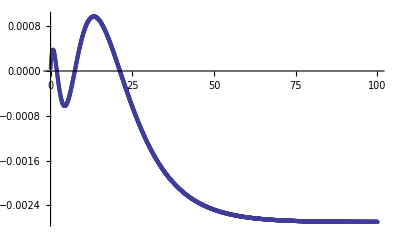

```mathematica
ListPlot[vec[[1;;2000]]]
```

### junk

```mathematica
Bisect[Critical,{0.1,1600.},0.8,0.9,10^(-6)]
```

Bisecting. Midpoint is 0.85

Bisecting. Midpoint is 0.825

Bisecting. Midpoint is 0.8375

Bisecting. Midpoint is 0.84375

Bisecting. Midpoint is 0.840625

Bisecting. Midpoint is 0.842188

Bisecting. Midpoint is 0.842969

Bisecting. Midpoint is 0.843359

Bisecting. Midpoint is 0.843164

Bisecting. Midpoint is 0.843262

Bisecting. Midpoint is 0.843311

Bisecting. Midpoint is 0.843286

Bisecting. Midpoint is 0.843274

Bisecting. Midpoint is 0.843268

Bisecting. Midpoint is 0.843271

Bisecting. Midpoint is 0.843272

Bisecting. Midpoint is 0.843273

Bisecting. Midpoint is 0.843273

{0.843273,0,1}

```mathematica
Bisect[Critical,{0.05,3200.},0.80,0.9,10^(-6)]
```

Bisecting. Midpoint is 0.85

Bisecting. Midpoint is 0.825

Bisecting. Midpoint is 0.8375

Bisecting. Midpoint is 0.84375

Bisecting. Midpoint is 0.840625

Bisecting. Midpoint is 0.842188

Bisecting. Midpoint is 0.841406

Bisecting. Midpoint is 0.841016

Bisecting. Midpoint is 0.84082

Bisecting. Midpoint is 0.840918

Bisecting. Midpoint is 0.840869

Bisecting. Midpoint is 0.840894

Bisecting. Midpoint is 0.840906

Bisecting. Midpoint is 0.8409

Bisecting. Midpoint is 0.840897

Bisecting. Midpoint is 0.840898

Bisecting. Midpoint is 0.840897

Bisecting. Midpoint is 0.840898

{0.840898,0,1}

```mathematica
%57[[1]]-(%41[[1]]-%57[[1]])
```

0.838523

### not junk

Bisection rootfinder, finding where a new negative eigenvalue appears. It returns not only the midpoint, but the number of negative eigenvalues at the low and high ends of the final range. This allows for a quick eyeball check if necessary to verify that there is in fact a zero where the function says there is.

```mathematica
Findlc[input_,i_,eps_]:=Module[{val,vah,lnegs,hnegs,res},
Print["***Beginning to calculate the "<>ToString[i]<>"th lambda, part "<>ToString[input[[1]]]];
res={input[[1]],Bisect[Critical,{input[[2,1]],input[[2,2]]},input[[3]],input[[4]],eps]};
Return[res]
]
```

```mathematica
FindlcTest[input_,i_,eps_]:=Module[{val,vah,lnegs,hnegs,res},
Print["***Beginning to calculate the "<>ToString[i]<>"th lambda, part "<>ToString[input[[1]]]];
val=Critical[input[[3]],{input[[2,1]],input[[2,2]]}];
vah=Critical[input[[4]],{input[[2,1]],input[[2,2]]}];
lnegs=CountNegs[val];
hnegs=CountNegs[vah];
If[lnegs<hnegs || (lnegs==hnegs && val[[1]]<vah[[1]]),(*doublechecks for zero*)
Print["Pass!"];
res={{input[[3]],input[[4]]},{"pass"}};
,(*else*)
Print["Fail!"];
res={{input[[3]],input[[4]]},{"fail"}};
];
Return[res]
]
```

This is the wrapper for parallel bisection. It makes sure that there is in fact a zero in the range, because the ρinf dependence means that sometimes the critical λ drifts out of the range. Any bisections done where there is no zero in the range would return the upper endpoint and be useless.

```mathematica
ListRandomize[list_]:=Module[{order,res},
order=Table[{RandomReal[],i},{i,1,Length[list]}];
order = Sort[order];
res=Table[list[[order[[i,2]]]],{i,1,Length[list]}];
Return[res]
]
```

This is a quick-and-dirty optimization for the parallel rootfinding. All it does is mix up the inputs so a kernel is less likely to get two long or two short calculations.

```mathematica
rhoinfs={40,80}; (*Scaling factors for λ*)
```

```mathematica
ranges={{467.4739234841014,467.4739234841014}}
```

{{467.474,467.474}}

### First calculations: refinement

```mathematica
SetDirectory["~/Desktop/Ellen/Thesis/Calculations/Angular Momentum/"]
```

/Network/Servers/Knowlton.local/Users/zphantom/Desktop/Ellen/Thesis/Calculations/Angular Momentum

```mathematica
l0data=Import["l0.csv"];
```

```mathematica
l0data[[2]]
```

{3.29715,0.0365915}

```mathematica
ranges=Table[{ranges[[i,1]]-3*ranges[[i,2]],ranges[[i,1]]},{i,1,Length[ranges]}]
```

```mathematica
ranges={{0.84,0.845},{3.22,3.24},{7.109750866889954,7.22},{12.612077236175537,12.827343463897705},{19.672054767608643,19.95009756088257},{28.301846981048584,28.642311573028564},{38.50174379348755,38.904447078704834},{50.26915788650513,50.73803377151489},{63.60709619522095,64.141761302948},{78.5151047706604,79.11599397659302},{94.99402666091919,95.66045904159546},{113.04274606704712,113.77575731277466},{132.66100358963013,133.46212148666382},{153.848379611969,154.7197699546814},{176.60773706436157,177.5473256111145},{200.9363875389099,201.94617700576782},{226.8368363380432,227.91507291793823},{254.30670976638794,255.45525884628296},{283.346556186676,284.56644201278687},{313.9577269554138,315.2480025291443},{346.1389317512512,347.5005784034729},{379.8906750679016,381.32391595840454},{415.21240758895874,416.71833848953247},{452.1055417060852,453.68311834335327},{490.56863832473755,492.21898794174194},{530.6023898124695,532.3256268501282},{572.2062392234802,574.0033192634583},{615.3815493583679,617.251362323761},{661,663},{706.4430651664734,708.460343837738+0.5},{754.3291535377502-0.5,756.4213309288025+0.5},{803.7868390083313-1,805.9526534080505+1},{854.8145480155945-1,857.0550780296326+1},{907.412929058075-2,909.7282948493958+2},{961.5815386772156-2,963.9725241661072+2}}
```

{{0.84,0.845},{3.22,3.24},{7.10975,7.22},{12.6121,12.8273},{19.6721,19.9501},{28.3018,28.6423},{38.5017,38.9044},{50.2692,50.738},{63.6071,64.1418},{78.5151,79.116},{94.994,95.6605},{113.043,113.776},{132.661,133.462},{153.848,154.72},{176.608,177.547},{200.936,201.946},{226.837,227.915},{254.307,255.455},{283.347,284.566},{313.958,315.248},{346.139,347.501},{379.891,381.324},{415.212,416.718},{452.106,453.683},{490.569,492.219},{530.602,532.326},{572.206,574.003},{615.382,617.251},{661,663},{706.443,708.96},{753.829,756.921},{802.787,806.953},{853.815,858.055},{905.413,911.728},{959.582,965.973}}

To reduce the number of failed rootfinding attempts, we refined the rough ranges above a bit more at different values of ρinf. The first gets down to a range of width 1/4, the second, a range of width 1/32.

```mathematica
inputslow=Table[{i,{0.1,25000},ranges[[i,1]],ranges[[i,2]]},{i,1,Length[ranges]}];
```

In order to deal with randomization later, the inputs are tagged with a number so they can be sorted again. This number is retained by Findlc.

```mathematica
inputslow=ListRandomize[inputslow];
```

```mathematica
DistributeDefinitions[Critical,Bisect,CountNegs,Findlc,FindlcTest,inputslow,l]
```

```mathematica
refinement=ParallelTable[FindlcTest[inputslow[[i]],i,0.25],{i,1,Length[inputslow]}]
```

***Beginning to calculate the 1th lambda, part 1

***Beginning to calculate the 3th lambda, part 3

***Beginning to calculate the 5th lambda, part 5

***Beginning to calculate the 7th lambda, part 7

***Beginning to calculate the 9th lambda, part 9

***Beginning to calculate the 15th lambda, part 15

***Beginning to calculate the 17th lambda, part 17

***Beginning to calculate the 11th lambda, part 11

***Beginning to calculate the 13th lambda, part 13

Pass!

***Beginning to calculate the 12th lambda, part 12

Pass!

***Beginning to calculate the 10th lambda, part 10

Pass!

***Beginning to calculate the 16th lambda, part 16

Pass!

***Beginning to calculate the 14th lambda, part 14

Pass!

***Beginning to calculate the 18th lambda, part 18

Pass!

***Beginning to calculate the 19th lambda, part 19

Pass!

***Beginning to calculate the 8th lambda, part 8

Pass!

***Beginning to calculate the 6th lambda, part 6

Pass!

***Beginning to calculate the 4th lambda, part 4

Pass!

***Beginning to calculate the 2th lambda, part 2

Pass!

***Beginning to calculate the 21th lambda, part 21

Pass!

***Beginning to calculate the 23th lambda, part 23

Pass!

***Beginning to calculate the 25th lambda, part 25

Pass!

***Beginning to calculate the 20th lambda, part 20

Pass!

***Beginning to calculate the 27th lambda, part 27

Pass!

***Beginning to calculate the 24th lambda, part 24

Pass!

***Beginning to calculate the 22th lambda, part 22

Pass!

***Beginning to calculate the 29th lambda, part 29

Pass!

***Beginning to calculate the 31th lambda, part 31

Pass!

***Beginning to calculate the 33th lambda, part 33

Pass!

***Beginning to calculate the 26th lambda, part 26

Pass!

***Beginning to calculate the 35th lambda, part 35

Pass!

Pass!

Pass!

«1 more identical outputs»

***Beginning to calculate the 32th lambda, part 32

Pass!

Pass!

***Beginning to calculate the 28th lambda, part 28

Fail!

***Beginning to calculate the 30th lambda, part 30

Pass!

***Beginning to calculate the 34th lambda, part 34

Pass!

Pass!

Pass!

«2 more identical outputs»

{{{0.84,0.845},{pass}},{{3.22,3.24},{pass}},{{7.10975,7.22},{pass}},{{12.6121,12.8273},{pass}},{{19.6721,19.9501},{pass}},{{28.3018,28.6423},{pass}},{{38.5017,38.9044},{pass}},{{50.2692,50.738},{pass}},{{63.6071,64.1418},{pass}},{{78.5151,79.116},{pass}},{{94.994,95.6605},{pass}},{{113.043,113.776},{pass}},{{132.661,133.462},{pass}},{{153.848,154.72},{pass}},{{176.608,177.547},{pass}},{{200.936,201.946},{pass}},{{226.837,227.915},{pass}},{{254.307,255.455},{pass}},{{283.347,284.566},{pass}},{{313.958,315.248},{pass}},{{346.139,347.501},{pass}},{{379.891,381.324},{pass}},{{415.212,416.718},{pass}},{{452.106,453.683},{pass}},{{490.569,492.219},{pass}},{{530.602,532.326},{pass}},{{572.206,574.003},{pass}},{{615.382,617.251},{pass}},{{660.127,662.07},{fail}},{{706.443,708.96},{pass}},{{753.829,756.921},{pass}},{{802.787,806.953},{pass}},{{853.815,858.055},{pass}},{{905.413,911.728},{pass}},{{959.582,965.973},{pass}}}

```mathematica
Critical[661,{0.1,25000}]
```

{-3.38496×10^-6,5.22011×10^-9,5.0546×10^-8,1.40537×10^-7,2.74203×10^-7,4.5051×10^-7,6.68546×10^-7,9.27557×10^-7,1.22692×10^-6,1.56612×10^-6,1.94472×10^-6,2.36234×10^-6,2.81865×10^-6,3.31335×10^-6,3.84617×10^-6,4.41689×10^-6,5.02527×10^-6,5.67113×10^-6,6.35428×10^-6,7.07454×10^-6,7.83176×10^-6,8.6258×10^-6,9.45652×10^-6,0.0000103238,0.0000112275}

```mathematica
Critical[663,{0.1,25000}]
```

{-3.68316×10^-6,-5.19049×10^-9,4.31109×10^-8,1.32532×10^-7,2.65423×10^-7,4.4078×10^-7,6.57735×10^-7,9.1557×10^-7,1.2137×10^-6,1.55163×10^-6,1.92894×10^-6,2.34528×10^-6,2.8003×10^-6,3.29373×10^-6,3.8253×10^-6,4.39477×10^-6,5.00193×10^-6,5.64659×10^-6,6.32855×10^-6,7.04765×10^-6,7.80373×10^-6,8.59664×10^-6,9.42625×10^-6,0.0000102924,0.000011195}

```mathematica
rangeshi=ranges
```

```mathematica
rangeshi={{0.8406,0.84063},{3.22,3.24},{7.109750866889954,7.22},{12.612077236175537,12.827343463897705},{19.672054767608643,19.95009756088257},{28.301846981048584,28.642311573028564},{38.50174379348755,38.904447078704834},{50.26915788650513,50.73803377151489},{63.60709619522095,64.141761302948},{78.5151047706604,79.11599397659302},{94.99402666091919,95.66045904159546},{113.04274606704712,113.77575731277466},{132.66100358963013,133.46212148666382},{153.848379611969,154.7197699546814},{176.60773706436157,177.5473256111145},{200.9363875389099,201.94617700576782},{226.8368363380432,227.91507291793823},{254.30670976638794,255.45525884628296},{283.346556186676,284.56644201278687},{313.9577269554138,315.2480025291443},{346.1389317512512,347.5005784034729},{379.8906750679016,381.32391595840454},{415.21240758895874,416.71833848953247},{452.1055417060852,453.68311834335327},{490.56863832473755,492.21898794174194},{530.6023898124695,532.3256268501282},{572.2062392234802,574.0033192634583},{615.3815493583679,617.251362323761},{660.1269812583923,662.0704569816589},{706.4430651664734,708.960343837738},{753.8291535377502,756.9213309288025},{802.7868390083313,806.9526534080505},{853.8145480155945,858.0550780296326},{905.412929058075,911.7282948493958},{959.5815386772156,965.9725241661072}}
```

{{0.8406,0.84063},{3.22,3.24},{7.10975,7.22},{12.6121,12.8273},{19.6721,19.9501},{28.3018,28.6423},{38.5017,38.9044},{50.2692,50.738},{63.6071,64.1418},{78.5151,79.116},{94.994,95.6605},{113.043,113.776},{132.661,133.462},{153.848,154.72},{176.608,177.547},{200.936,201.946},{226.837,227.915},{254.307,255.455},{283.347,284.566},{313.958,315.248},{346.139,347.501},{379.891,381.324},{415.212,416.718},{452.106,453.683},{490.569,492.219},{530.602,532.326},{572.206,574.003},{615.382,617.251},{660.127,662.07},{706.443,708.96},{753.829,756.921},{802.787,806.953},{853.815,858.055},{905.413,911.728},{959.582,965.973}}

```mathematica
inputshigh=Table[{i,{0.05,50000},rangeshi[[i,1]],rangeshi[[i,2]]},{i,1,Length[ranges]}];
```

```mathematica
DistributeDefinitions[inputshigh]
```

```mathematica
refinement=ParallelTable[FindlcTest[inputslow[[i]],i,0.25],{i,1,Length[inputshigh]}]
```

***Beginning to calculate the 1th lambda, part 1

***Beginning to calculate the 3th lambda, part 3

***Beginning to calculate the 5th lambda, part 5

***Beginning to calculate the 7th lambda, part 7

***Beginning to calculate the 9th lambda, part 9

***Beginning to calculate the 11th lambda, part 11

***Beginning to calculate the 13th lambda, part 13

***Beginning to calculate the 15th lambda, part 15

***Beginning to calculate the 17th lambda, part 17

$Aborted

```mathematica
Critical[708.460343837738+0.5,{0.1,25000}]
```

{-3.14414×10^-6,-1.53869×10^-9,4.66068×10^-8,1.38849×10^-7,2.75578×10^-7,4.55624×10^-7,6.77993×10^-7,9.41882×10^-7,1.24664×10^-6,1.59172×10^-6,1.97668×10^-6,2.40109×10^-6,2.86462×10^-6,3.36695×10^-6,3.90779×10^-6,4.48689×10^-6,5.10402×10^-6,5.75896×10^-6,6.45151×10^-6,7.1815×10^-6,7.94875×10^-6,8.75311×10^-6,9.59443×10^-6,0.0000104726,0.0000113874}

```mathematica
ins=Table[0.84058+i*10^(-5),{i,1,18}]
```

{0.84059,0.8406,0.84061,0.84062,0.84063,0.84064,0.84065,0.84066,0.84067,0.84068,0.84069,0.8407,0.84071,0.84072,0.84073,0.84074,0.84075,0.84076}

```mathematica
DistributeDefinitions[ins]
```

```mathematica
ParallelTable[Critical[ins[[i]],{0.05,50000}],{i,1,Length[ins]}]
```

{{1.37008×10^-9,9.30199×10^-9,2.5098×10^-8,4.8787×10^-8,8.03713×10^-8,1.19851×10^-7,1.67227×10^-7,2.22499×10^-7,2.85667×10^-7,3.5673×10^-7,4.3569×10^-7,5.22545×10^-7,6.17297×10^-7,7.19944×10^-7,8.30487×10^-7,9.48926×10^-7,1.07526×10^-6,1.20949×10^-6,1.35162×10^-6,1.50164×10^-6,1.65956×10^-6,1.82538×10^-6,1.99909×10^-6,2.18069×10^-6,2.3702×10^-6},{9.92687×10^-10,8.88864×10^-9,2.46805×10^-8,4.83684×10^-8,7.99522×10^-8,1.19432×10^-7,1.66808×10^-7,2.22079×10^-7,2.85247×10^-7,3.5631×10^-7,4.3527×10^-7,5.22125×10^-7,6.16877×10^-7,7.19524×10^-7,8.30067×10^-7,9.48507×10^-7,1.07484×10^-6,1.20907×10^-6,1.3512×10^-6,1.50122×10^-6,1.65914×10^-6,1.82496×10^-6,1.99867×10^-6,2.18027×10^-6,2.36978×10^-6},{5.25999×10^-10,8.46547×10^-9,2.42595×10^-8,4.79479×10^-8,7.95319×10^-8,1.19012×10^-7,1.66388×10^-7,2.21659×10^-7,2.84827×10^-7,3.5589×10^-7,4.3485×10^-7,5.21705×10^-7,6.16457×10^-7,7.19104×10^-7,8.29647×10^-7,9.48087×10^-7,1.07442×10^-6,1.20865×10^-6,1.35078×10^-6,1.5008×10^-6,1.65872×10^-6,1.82454×10^-6,1.99825×10^-6,2.17985×10^-6,2.36936×10^-6},{-5.14934×10^-11,8.04257×10^-9,2.38386×10^-8,4.75275×10^-8,7.91118×10^-8,1.18592×10^-7,1.65968×10^-7,2.21239×10^-7,2.84407×10^-7,3.5547×10^-7,4.3443×10^-7,5.21285×10^-7,6.16037×10^-7,7.18684×10^-7,8.29228×10^-7,9.47667×10^-7,1.074×10^-6,1.20823×10^-6,1.35036×10^-6,1.50038×10^-6,1.6583×10^-6,1.82412×10^-6,1.99783×10^-6,2.17943×10^-6,2.36894×10^-6},{-7.63097×10^-10,7.63155×10^-9,2.34217×10^-8,4.71091×10^-8,7.86928×10^-8,1.18172×10^-7,1.65548×10^-7,2.2082×10^-7,2.83987×10^-7,3.55051×10^-7,4.3401×10^-7,5.20866×10^-7,6.15617×10^-7,7.18264×10^-7,8.28808×10^-7,9.47247×10^-7,1.07358×10^-6,1.20781×10^-6,1.34994×10^-6,1.49996×10^-6,1.65788×10^-6,1.8237×10^-6,1.99741×10^-6,2.17902×10^-6,2.36852×10^-6},{-1.63186×10^-9,7.24379×10^-9,2.30127×10^-8,4.66947×10^-8,7.82762×10^-8,1.17755×10^-7,1.6513×10^-7,2.20401×10^-7,2.83568×10^-7,3.54632×10^-7,4.33591×10^-7,5.20446×10^-7,6.15198×10^-7,7.17845×10^-7,8.28388×10^-7,9.46827×10^-7,1.07316×10^-6,1.20739×10^-6,1.34952×10^-6,1.49954×10^-6,1.65746×10^-6,1.82328×10^-6,1.99699×10^-6,2.1786×10^-6,2.3681×10^-6},{-2.67821×10^-9,6.88842×10^-9,2.26152×10^-8,4.62862×10^-8,7.78632×10^-8,1.17339×10^-7,1.64713×10^-7,2.19984×10^-7,2.8315×10^-7,3.54213×10^-7,4.33172×10^-7,5.20028×10^-7,6.14779×10^-7,7.17426×10^-7,8.27969×10^-7,9.46408×10^-7,1.07274×10^-6,1.20697×10^-6,1.3491×10^-6,1.49912×10^-6,1.65704×10^-6,1.82286×10^-6,1.99657×10^-6,2.17818×10^-6,2.36768×10^-6},{-3.91828×10^-9,6.57087×10^-9,2.22325×10^-8,4.58852×10^-8,7.74547×10^-8,1.16927×10^-7,1.64299×10^-7,2.19568×10^-7,2.82734×10^-7,3.53796×10^-7,4.32755×10^-7,5.19609×10^-7,6.1436×10^-7,7.17007×10^-7,8.2755×10^-7,9.45989×10^-7,1.07232×10^-6,1.20656×10^-6,1.34868×10^-6,1.49871×10^-6,1.65662×10^-6,1.82244×10^-6,1.99615×10^-6,2.17776×10^-6,2.36726×10^-6},{-5.36334×10^-9,6.29265×10^-9,2.1867×10^-8,4.54935×10^-8,7.7052×10^-8,1.16519×10^-7,1.63887×10^-7,2.19154×10^-7,2.82319×10^-7,3.5338×10^-7,4.32338×10^-7,5.19192×10^-7,6.13943×10^-7,7.16589×10^-7,8.27132×10^-7,9.45571×10^-7,1.07191×10^-6,1.20614×10^-6,1.34826×10^-6,1.49829×10^-6,1.6562×10^-6,1.82202×10^-6,1.99573×10^-6,2.17734×10^-6,2.36684×10^-6},{-7.0205×10^-9,6.05209×10^-9,2.15207×10^-8,4.51125×10^-8,7.6656×10^-8,1.16115×10^-7,1.63479×10^-7,2.18743×10^-7,2.81906×10^-7,3.52966×10^-7,4.31923×10^-7,5.18776×10^-7,6.13526×10^-7,7.16172×10^-7,8.26715×10^-7,9.45153×10^-7,1.07149×10^-6,1.20572×10^-6,1.34784×10^-6,1.49787×10^-6,1.65579×10^-6,1.8216×10^-6,1.99531×10^-6,2.17692×10^-6,2.36642×10^-6},{-8.8938×10^-9,5.8456×10^-9,2.11948×10^-8,4.47433×10^-8,7.62674×10^-8,1.15716×10^-7,1.63074×10^-7,2.18335×10^-7,2.81495×10^-7,3.52553×10^-7,4.31509×10^-7,5.18361×10^-7,6.1311×10^-7,7.15756×10^-7,8.26298×10^-7,9.44736×10^-7,1.07107×10^-6,1.2053×10^-6,1.34743×10^-6,1.49745×10^-6,1.65537×10^-6,1.82118×10^-6,1.99489×10^-6,2.1765×10^-6,2.366×10^-6},{-1.09854×10^-8,5.6688×10^-9,2.08898×10^-8,4.43869×10^-8,7.58873×10^-8,1.15324×10^-7,1.62674×10^-7,2.1793×10^-7,2.81087×10^-7,3.52143×10^-7,4.31097×10^-7,5.17948×10^-7,6.12696×10^-7,7.15341×10^-7,8.25882×10^-7,9.4432×10^-7,1.07065×10^-6,1.20488×10^-6,1.34701×10^-6,1.49703×10^-6,1.65495×10^-6,1.82076×10^-6,1.99447×10^-6,2.17608×10^-6,2.36558×10^-6},{-1.32962×10^-8,5.51726×10^-9,2.06058×10^-8,4.4044×10^-8,7.55161×10^-8,1.14937×10^-7,1.62278×10^-7,2.17528×10^-7,2.80681×10^-7,3.51734×10^-7,4.30686×10^-7,5.17536×10^-7,6.12283×10^-7,7.14927×10^-7,8.25467×10^-7,9.43904×10^-7,1.07024×10^-6,1.20447×10^-6,1.34659×10^-6,1.49661×10^-6,1.65453×10^-6,1.82035×10^-6,1.99406×10^-6,2.17566×10^-6,2.36517×10^-6},{-1.58269×10^-8,5.38693×10^-9,2.03421×10^-8,4.37151×10^-8,7.51545×10^-8,1.14558×10^-7,1.61888×10^-7,2.17131×10^-7,2.80279×10^-7,3.51328×10^-7,4.30278×10^-7,5.17126×10^-7,6.11871×10^-7,7.14514×10^-7,8.25054×10^-7,9.4349×10^-7,1.06982×10^-6,1.20405×10^-6,1.34618×10^-6,1.4962×10^-6,1.65412×10^-6,1.81993×10^-6,1.99364×10^-6,2.17525×10^-6,2.36475×10^-6},{-1.85777×10^-8,5.27431×10^-9,2.0098×10^-8,4.34005×10^-8,7.4803×10^-8,1.14185×10^-7,1.61503×10^-7,2.16737×10^-7,2.7988×10^-7,3.50925×10^-7,4.29872×10^-7,5.16717×10^-7,6.11461×10^-7,7.14103×10^-7,8.24641×10^-7,9.43076×10^-7,1.06941×10^-6,1.20364×10^-6,1.34576×10^-6,1.49578×10^-6,1.6537×10^-6,1.81951×10^-6,1.99322×10^-6,2.17483×10^-6,2.36433×10^-6},{-2.15485×10^-8,5.17644×10^-9,1.98723×10^-8,4.31002×10^-8,7.44619×10^-8,1.1382×10^-7,1.61123×10^-7,2.16348×10^-7,2.79484×10^-7,3.50525×10^-7,4.29468×10^-7,5.16311×10^-7,6.11053×10^-7,7.13693×10^-7,8.2423×10^-7,9.42664×10^-7,1.069×10^-6,1.20322×10^-6,1.34535×10^-6,1.49537×10^-6,1.65328×10^-6,1.8191×10^-6,1.99281×10^-6,2.17441×10^-6,2.36391×10^-6},{-2.47395×10^-8,5.0909×10^-9,1.9664×10^-8,4.28141×10^-8,7.41314×10^-8,1.13464×10^-7,1.6075×10^-7,2.15964×10^-7,2.79093×10^-7,3.50128×10^-7,4.29067×10^-7,5.15907×10^-7,6.10647×10^-7,7.13284×10^-7,8.2382×10^-7,9.42253×10^-7,1.06858×10^-6,1.20281×10^-6,1.34493×10^-6,1.49495×10^-6,1.65287×10^-6,1.81868×10^-6,1.99239×10^-6,2.174×10^-6,2.3635×10^-6},{-2.81506×10^-8,5.01568×10^-9,1.94718×10^-8,4.2542×10^-8,7.38118×10^-8,1.13115×10^-7,1.60383×10^-7,2.15585×10^-7,2.78705×10^-7,3.49735×10^-7,4.28669×10^-7,5.15506×10^-7,6.10242×10^-7,7.12878×10^-7,8.23412×10^-7,9.41844×10^-7,1.06817×10^-6,1.2024×10^-6,1.34452×10^-6,1.49454×10^-6,1.65246×10^-6,1.81827×10^-6,1.99198×10^-6,2.17358×10^-6,2.36308×10^-6}}

```mathematica
refinement=Sort[refinement];
```

```mathematica
refinement={{3,{ranges[[1,1]],2}}};
```

```mathematica
inputshigh=Table[{i,rhoinfs[[2]]*refinement[[i,2,1]],refinement[[i,2,1]]-0.75,refinement[[i,2,1]]+0.75},{i,1,Length[refinement]}];
```

```mathematica
inputshigh=ListRandomize[inputshigh]
```

```mathematica
DistributeDefinitions[inputshigh]
```

```mathematica
refinement2=ParallelTable[Findlc[inputshigh[[i]],i,1/32.],{i,1,Length[inputshigh]}]
```

```mathematica
refinement2=Sort[refinement2];
```

```mathematica
refinement2={{3,{ranges[[1,1]],2}}};
```

### Second calculation: lcs for real

```mathematica
ref1ins= Table[{i,rhoinfs[[1]]*refinement[[i,2,1]],refinement[[i,2,1]]-1.,refinement[[i,2,1]]+1.},{i,1,Length[refinement]}];
```

```mathematica
ref2ins=Table[{i+Length[ref1ins],rhoinfs[[2]]*refinement2[[i,2,1]],refinement2[[i,2,1]]-1.,refinement2[[i,2,1]]+1.},{i,1,Length[refinement2]}];
```

And now we combine the refined ranges, make input lists out of them, and find the values of the λcs to within 10^-6.

```mathematica
newins=Join[inputslow,inputshigh];
```

```mathematica
newins=ListRandomize[newins];
```

```mathematica
DistributeDefinitions[newins,Findlc]
```

```mathematica
lcs=ParallelTable[Findlc[newins[[i]],i,10^-6],{i,1,Length[newins]}]
```

***Beginning to calculate the 1th lambda, part 1

***Beginning to calculate the 4th lambda, part 14

***Beginning to calculate the 7th lambda, part 20

***Beginning to calculate the 10th lambda, part 18

***Beginning to calculate the 13th lambda, part 26

***Beginning to calculate the 16th lambda, part 6

***Beginning to calculate the 19th lambda, part 11

***Beginning to calculate the 22th lambda, part 2

***Beginning to calculate the 25th lambda, part 30

Bisecting. Midpoint is 0.8425

Bisecting. Midpoint is 154.284

Bisecting. Midpoint is 314.603

Bisecting. Midpoint is 254.881

Bisecting. Midpoint is 531.464

Bisecting. Midpoint is 28.4721

Bisecting. Midpoint is 95.3272

Bisecting. Midpoint is 3.23

Bisecting. Midpoint is 707.702

Bisecting. Midpoint is 531.895

Bisecting. Midpoint is 3.225

Bisecting. Midpoint is 708.331

Bisecting. Midpoint is 255.168

Bisecting. Midpoint is 0.84375

Bisecting. Midpoint is 532.11

Bisecting. Midpoint is 3.2275

Bisecting. Midpoint is 708.646

Bisecting. Midpoint is 255.025

Bisecting. Midpoint is 532.218

Bisecting. Midpoint is 0.843125

Bisecting. Midpoint is 3.22625

Bisecting. Midpoint is 95.1606

Bisecting. Midpoint is 708.803

Bisecting. Midpoint is 532.164

Bisecting. Midpoint is 28.387

Bisecting. Midpoint is 254.953

Bisecting. Midpoint is 3.22688

Bisecting. Midpoint is 0.842813

Bisecting. Midpoint is 532.137

Bisecting. Midpoint is 708.724

Bisecting. Midpoint is 3.22656

Bisecting. Midpoint is 532.151

Bisecting. Midpoint is 254.989

Bisecting. Midpoint is 314.925

Bisecting. Midpoint is 154.066

Bisecting. Midpoint is 708.685

Bisecting. Midpoint is 0.842656

Bisecting. Midpoint is 3.22672

Bisecting. Midpoint is 532.144

Bisecting. Midpoint is 95.2439

Bisecting. Midpoint is 255.007

Bisecting. Midpoint is 532.147

Bisecting. Midpoint is 3.2268

Bisecting. Midpoint is 708.665

Bisecting. Midpoint is 28.4295

Bisecting. Midpoint is 0.842734

Bisecting. Midpoint is 532.146

Bisecting. Midpoint is 255.016

Bisecting. Midpoint is 3.22676

Bisecting. Midpoint is 708.656

Bisecting. Midpoint is 532.145

Bisecting. Midpoint is 0.842695

Bisecting. Midpoint is 3.22678

Bisecting. Midpoint is 255.011

Bisecting. Midpoint is 532.145

Bisecting. Midpoint is 708.66

Bisecting. Midpoint is 95.2856

Bisecting. Midpoint is 3.22679

Bisecting. Midpoint is 154.175

Bisecting. Midpoint is 532.145

Bisecting. Midpoint is 255.009

Bisecting. Midpoint is 0.842715

Bisecting. Midpoint is 314.764

Bisecting. Midpoint is 708.663

Bisecting. Midpoint is 3.22679

Bisecting. Midpoint is 28.4082

Bisecting. Midpoint is 532.145

Bisecting. Midpoint is 255.008

Bisecting. Midpoint is 708.662

Bisecting. Midpoint is 0.842705

Bisecting. Midpoint is 3.22679

Bisecting. Midpoint is 532.145

Bisecting. Midpoint is 95.2648

Bisecting. Midpoint is 708.661

Bisecting. Midpoint is 255.008

Bisecting. Midpoint is 3.2268

Bisecting. Midpoint is 532.145

Bisecting. Midpoint is 0.84271

Bisecting. Midpoint is 708.661

Bisecting. Midpoint is 532.145

Bisecting. Midpoint is 255.008

Bisecting. Midpoint is 3.2268

Bisecting. Midpoint is 28.4189

Bisecting. Midpoint is 0.842712

Bisecting. Midpoint is 708.662

Bisecting. Midpoint is 532.145

Bisecting. Midpoint is 154.23

Bisecting. Midpoint is 255.008

Bisecting. Midpoint is 314.684

Bisecting. Midpoint is 3.2268

Bisecting. Midpoint is 95.2752

Bisecting. Midpoint is 532.145

Bisecting. Midpoint is 708.661

Bisecting. Midpoint is 0.842714

Bisecting. Midpoint is 255.008

Bisecting. Midpoint is 532.145

***Beginning to calculate the 23th lambda, part 22

Bisecting. Midpoint is 380.607

Bisecting. Midpoint is 708.661

Bisecting. Midpoint is 532.145

Bisecting. Midpoint is 0.842713

Bisecting. Midpoint is 28.4242

Bisecting. Midpoint is 255.008

Bisecting. Midpoint is 380.966

Bisecting. Midpoint is 532.145

Bisecting. Midpoint is 708.661

Bisecting. Midpoint is 380.786

Bisecting. Midpoint is 255.008

Bisecting. Midpoint is 0.842713

Bisecting. Midpoint is 95.27

***Beginning to calculate the 14th lambda, part 34

Bisecting. Midpoint is 908.571

Bisecting. Midpoint is 708.661

Bisecting. Midpoint is 380.876

Bisecting. Midpoint is 910.149

Bisecting. Midpoint is 154.257

Bisecting. Midpoint is 314.643

Bisecting. Midpoint is 380.921

Bisecting. Midpoint is 255.008

Bisecting. Midpoint is 708.661

Bisecting. Midpoint is 910.939

***Beginning to calculate the 2th lambda, part 9

Bisecting. Midpoint is 63.8744

Bisecting. Midpoint is 380.943

Bisecting. Midpoint is 28.4269

Bisecting. Midpoint is 255.008

Bisecting. Midpoint is 708.661

Bisecting. Midpoint is 910.544

Bisecting. Midpoint is 380.954

Bisecting. Midpoint is 95.2674

Bisecting. Midpoint is 910.742

Bisecting. Midpoint is 255.008

Bisecting. Midpoint is 708.661

Bisecting. Midpoint is 380.949

Bisecting. Midpoint is 910.643

Bisecting. Midpoint is 380.946

Bisecting. Midpoint is 255.008

Bisecting. Midpoint is 708.661

Bisecting. Midpoint is 910.594

Bisecting. Midpoint is 380.945

Bisecting. Midpoint is 28.4282

Bisecting. Midpoint is 708.661

Bisecting. Midpoint is 154.243

Bisecting. Midpoint is 380.944

Bisecting. Midpoint is 255.008

Bisecting. Midpoint is 910.569

Bisecting. Midpoint is 314.623

Bisecting. Midpoint is 95.2661

Bisecting. Midpoint is 380.944

Bisecting. Midpoint is 63.7408

Bisecting. Midpoint is 910.581

Bisecting. Midpoint is 255.008

***Beginning to calculate the 26th lambda, part 25

Bisecting. Midpoint is 491.394

Bisecting. Midpoint is 380.944

Bisecting. Midpoint is 910.575

Bisecting. Midpoint is 491.806

Bisecting. Midpoint is 910.572

Bisecting. Midpoint is 380.945

***Beginning to calculate the 11th lambda, part 25

Bisecting. Midpoint is 491.394

Bisecting. Midpoint is 95.2667

Bisecting. Midpoint is 910.57

Bisecting. Midpoint is 492.013

Bisecting. Midpoint is 28.4275

Bisecting. Midpoint is 380.945

Bisecting. Midpoint is 910.571

Bisecting. Midpoint is 380.945

Bisecting. Midpoint is 491.91

Bisecting. Midpoint is 154.236

Bisecting. Midpoint is 910.571

Bisecting. Midpoint is 380.945

Bisecting. Midpoint is 314.633

Bisecting. Midpoint is 491.961

Bisecting. Midpoint is 63.8076

Bisecting. Midpoint is 910.571

Bisecting. Midpoint is 380.945

Bisecting. Midpoint is 95.267

Bisecting. Midpoint is 491.987

Bisecting. Midpoint is 910.571

Bisecting. Midpoint is 380.945

Bisecting. Midpoint is 28.4279

Bisecting. Midpoint is 910.571

Bisecting. Midpoint is 380.945

Bisecting. Midpoint is 491.974

Bisecting. Midpoint is 491.806

Bisecting. Midpoint is 910.571

Bisecting. Midpoint is 380.945

Bisecting. Midpoint is 491.968

Bisecting. Midpoint is 910.571

Bisecting. Midpoint is 380.945

Bisecting. Midpoint is 95.2672

Bisecting. Midpoint is 154.233

Bisecting. Midpoint is 910.571

Bisecting. Midpoint is 491.971

Bisecting. Midpoint is 314.628

***Beginning to calculate the 24th lambda, part 9

Bisecting. Midpoint is 63.8744

Bisecting. Midpoint is 910.571

Bisecting. Midpoint is 28.4277

Bisecting. Midpoint is 63.841

Bisecting. Midpoint is 491.972

Bisecting. Midpoint is 63.7408

Bisecting. Midpoint is 910.571

Bisecting. Midpoint is 491.973

Bisecting. Midpoint is 63.8076

Bisecting. Midpoint is 910.571

Bisecting. Midpoint is 95.2673

Bisecting. Midpoint is 910.571

Bisecting. Midpoint is 491.6

Bisecting. Midpoint is 63.841

Bisecting. Midpoint is 491.974

Bisecting. Midpoint is 63.8243

Bisecting. Midpoint is 491.974

***Beginning to calculate the 15th lambda, part 4

Bisecting. Midpoint is 12.7197

Bisecting. Midpoint is 28.4276

Bisecting. Midpoint is 63.8327

Bisecting. Midpoint is 154.231

Bisecting. Midpoint is 491.974

Bisecting. Midpoint is 314.626

Bisecting. Midpoint is 63.8368

Bisecting. Midpoint is 95.2672

Bisecting. Midpoint is 63.8243

Bisecting. Midpoint is 491.974

Bisecting. Midpoint is 63.8347

Bisecting. Midpoint is 63.8358

Bisecting. Midpoint is 491.974

Bisecting. Midpoint is 28.4277

Bisecting. Midpoint is 12.6659

Bisecting. Midpoint is 491.974

Bisecting. Midpoint is 63.8353

Bisecting. Midpoint is 491.497

Bisecting. Midpoint is 95.2673

Bisecting. Midpoint is 491.974

Bisecting. Midpoint is 63.835

Bisecting. Midpoint is 154.232

Bisecting. Midpoint is 63.8351

Bisecting. Midpoint is 491.974

Bisecting. Midpoint is 314.624

Bisecting. Midpoint is 63.8352

Bisecting. Midpoint is 28.4277

Bisecting. Midpoint is 491.974

Bisecting. Midpoint is 63.8159

Bisecting. Midpoint is 95.2673

Bisecting. Midpoint is 63.8352

Bisecting. Midpoint is 12.6928

Bisecting. Midpoint is 491.974

Bisecting. Midpoint is 63.8352

Bisecting. Midpoint is 491.974

Bisecting. Midpoint is 63.8351

Bisecting. Midpoint is 491.549

Bisecting. Midpoint is 63.8351

Bisecting. Midpoint is 154.232

***Beginning to calculate the 27th lambda, part 30

Bisecting. Midpoint is 707.702

Bisecting. Midpoint is 28.4277

Bisecting. Midpoint is 95.2673

Bisecting. Midpoint is 63.8351

Bisecting. Midpoint is 12.6793

Bisecting. Midpoint is 314.625

Bisecting. Midpoint is 63.8351

Bisecting. Midpoint is 63.8201

Bisecting. Midpoint is 63.8351

Bisecting. Midpoint is 63.8351

Bisecting. Midpoint is 95.2673

Bisecting. Midpoint is 708.331

Bisecting. Midpoint is 28.4277

Bisecting. Midpoint is 491.574

***Beginning to calculate the 28th lambda, part 32

Bisecting. Midpoint is 804.87

Bisecting. Midpoint is 154.232

Bisecting. Midpoint is 12.6861

Bisecting. Midpoint is 805.911

Bisecting. Midpoint is 314.625

Bisecting. Midpoint is 806.432

Bisecting. Midpoint is 95.2673

Bisecting. Midpoint is 63.818

Bisecting. Midpoint is 806.692

Bisecting. Midpoint is 28.4277

Bisecting. Midpoint is 708.016

Bisecting. Midpoint is 806.562

Bisecting. Midpoint is 806.497

Bisecting. Midpoint is 12.6894

Bisecting. Midpoint is 806.464

Bisecting. Midpoint is 491.561

Bisecting. Midpoint is 154.232

Bisecting. Midpoint is 95.2673

Bisecting. Midpoint is 806.448

Bisecting. Midpoint is 314.625

Bisecting. Midpoint is 28.4277

Bisecting. Midpoint is 806.44

Bisecting. Midpoint is 707.859

Bisecting. Midpoint is 63.817

Bisecting. Midpoint is 806.436

Bisecting. Midpoint is 806.434

Bisecting. Midpoint is 12.6878

Bisecting. Midpoint is 95.2673

Bisecting. Midpoint is 806.435

Bisecting. Midpoint is 806.435

Bisecting. Midpoint is 28.4277

Bisecting. Midpoint is 491.555

Bisecting. Midpoint is 806.436

Bisecting. Midpoint is 154.232

Bisecting. Midpoint is 806.436

Bisecting. Midpoint is 707.938

Bisecting. Midpoint is 314.625

Bisecting. Midpoint is 806.436

Bisecting. Midpoint is 12.6886

Bisecting. Midpoint is 806.436

Bisecting. Midpoint is 63.8175

Bisecting. Midpoint is 806.436

***Beginning to calculate the 20th lambda, part 7

Bisecting. Midpoint is 38.7031

Bisecting. Midpoint is 806.436

Bisecting. Midpoint is 28.4277

Bisecting. Midpoint is 806.436

Bisecting. Midpoint is 38.6024

Bisecting. Midpoint is 806.436

Bisecting. Midpoint is 38.6528

Bisecting. Midpoint is 707.898

Bisecting. Midpoint is 806.436

Bisecting. Midpoint is 38.6779

Bisecting. Midpoint is 12.6882

Bisecting. Midpoint is 491.558

Bisecting. Midpoint is 806.436

Bisecting. Midpoint is 154.232

Bisecting. Midpoint is 38.6653

Bisecting. Midpoint is 314.625

***Beginning to calculate the 29th lambda, part 28

Bisecting. Midpoint is 616.316

Bisecting. Midpoint is 38.659

Bisecting. Midpoint is 616.784

Bisecting. Midpoint is 63.8173

Bisecting. Midpoint is 38.6622

Bisecting. Midpoint is 617.018

Bisecting. Midpoint is 617.134

Bisecting. Midpoint is 38.6638

***Beginning to calculate the 17th lambda, part 29

Bisecting. Midpoint is 661.099

Bisecting. Midpoint is 617.193

Bisecting. Midpoint is 707.879

Bisecting. Midpoint is 12.688

Bisecting. Midpoint is 38.663

Bisecting. Midpoint is 617.222

Bisecting. Midpoint is 38.6626

Bisecting. Midpoint is 617.237

Bisecting. Midpoint is 38.6628

Bisecting. Midpoint is 491.56

Bisecting. Midpoint is 617.229

Bisecting. Midpoint is 154.232

Bisecting. Midpoint is 617.233

Bisecting. Midpoint is 314.625

Bisecting. Midpoint is 661.585

Bisecting. Midpoint is 38.6627

Bisecting. Midpoint is 617.235

Bisecting. Midpoint is 63.8174

Bisecting. Midpoint is 38.6626

Bisecting. Midpoint is 617.234

Bisecting. Midpoint is 12.6879

Bisecting. Midpoint is 707.869

Bisecting. Midpoint is 617.234

Bisecting. Midpoint is 38.6626

Bisecting. Midpoint is 617.235

Bisecting. Midpoint is 38.6626

Bisecting. Midpoint is 617.235

Bisecting. Midpoint is 661.342

Bisecting. Midpoint is 38.6626

Bisecting. Midpoint is 617.235

Bisecting. Midpoint is 38.6626

Bisecting. Midpoint is 617.235

Bisecting. Midpoint is 617.235

Bisecting. Midpoint is 491.561

Bisecting. Midpoint is 38.6626

Bisecting. Midpoint is 154.232

Bisecting. Midpoint is 12.6878

Bisecting. Midpoint is 314.625

Bisecting. Midpoint is 617.235

Bisecting. Midpoint is 38.6626

Bisecting. Midpoint is 707.864

Bisecting. Midpoint is 617.235

Bisecting. Midpoint is 63.8173

Bisecting. Midpoint is 661.463

Bisecting. Midpoint is 38.6626

Bisecting. Midpoint is 617.235

Bisecting. Midpoint is 617.235

***Beginning to calculate the 21th lambda, part 6

Bisecting. Midpoint is 28.4721

Bisecting. Midpoint is 617.235

Bisecting. Midpoint is 28.387

Bisecting. Midpoint is 12.6878

***Beginning to calculate the 30th lambda, part 1

Bisecting. Midpoint is 0.840615

Bisecting. Midpoint is 28.4295

Bisecting. Midpoint is 661.402

Bisecting. Midpoint is 707.866

Bisecting. Midpoint is 28.4508

Bisecting. Midpoint is 491.56

Bisecting. Midpoint is 314.625

Bisecting. Midpoint is 154.232

Bisecting. Midpoint is 28.4402

Bisecting. Midpoint is 63.8173

Bisecting. Midpoint is 28.4348

Bisecting. Midpoint is 0.840623

Bisecting. Midpoint is 12.6878

Bisecting. Midpoint is 28.4322

Bisecting. Midpoint is 661.433

Bisecting. Midpoint is 28.4335

Bisecting. Midpoint is 28.4342

Bisecting. Midpoint is 707.868

Bisecting. Midpoint is 0.840619

Bisecting. Midpoint is 28.4345

Bisecting. Midpoint is 661.448

Bisecting. Midpoint is 314.625

Bisecting. Midpoint is 28.4343

Bisecting. Midpoint is 491.56

Bisecting. Midpoint is 12.6879

Bisecting. Midpoint is 28.4344

Bisecting. Midpoint is 154.232

Bisecting. Midpoint is 28.4344

Bisecting. Midpoint is 63.8173

Bisecting. Midpoint is 0.840621

Bisecting. Midpoint is 28.4344

Bisecting. Midpoint is 707.868

Bisecting. Midpoint is 661.456

Bisecting. Midpoint is 28.4344

Bisecting. Midpoint is 12.6879

Bisecting. Midpoint is 28.4344

Bisecting. Midpoint is 28.4344

Bisecting. Midpoint is 0.84062

Bisecting. Midpoint is 28.4344

Bisecting. Midpoint is 314.625

Bisecting. Midpoint is 491.56

Bisecting. Midpoint is 28.4344

Bisecting. Midpoint is 661.452

Bisecting. Midpoint is 707.869

Bisecting. Midpoint is 28.4344

Bisecting. Midpoint is 154.232

Bisecting. Midpoint is 63.8173

Bisecting. Midpoint is 12.6879

***Beginning to calculate the 31th lambda, part 31

Bisecting. Midpoint is 755.375

Bisecting. Midpoint is 0.840619

Bisecting. Midpoint is 756.148

Bisecting. Midpoint is 661.454

Bisecting. Midpoint is 756.535

Bisecting. Midpoint is 756.728

Bisecting. Midpoint is 314.625

Bisecting. Midpoint is 707.868

Bisecting. Midpoint is 491.56

Bisecting. Midpoint is 756.825

Bisecting. Midpoint is 12.6879

Bisecting. Midpoint is 756.776

Bisecting. Midpoint is 661.455

Bisecting. Midpoint is 154.232

Bisecting. Midpoint is 63.8173

***Beginning to calculate the 34th lambda, part 10

Bisecting. Midpoint is 78.8155

Bisecting. Midpoint is 756.752

Bisecting. Midpoint is 756.764

Bisecting. Midpoint is 756.758

Bisecting. Midpoint is 707.868

Bisecting. Midpoint is 12.6879

Bisecting. Midpoint is 756.755

Bisecting. Midpoint is 661.455

Bisecting. Midpoint is 314.625

Bisecting. Midpoint is 78.6653

Bisecting. Midpoint is 756.754

Bisecting. Midpoint is 491.56

Bisecting. Midpoint is 756.754

Bisecting. Midpoint is 756.755

Bisecting. Midpoint is 63.8173

Bisecting. Midpoint is 707.868

Bisecting. Midpoint is 661.455

Bisecting. Midpoint is 756.755

Bisecting. Midpoint is 78.7404

Bisecting. Midpoint is 756.755

***Beginning to calculate the 5th lambda, part 20

Bisecting. Midpoint is 314.603

Bisecting. Midpoint is 756.755

***Beginning to calculate the 37th lambda, part 10

Bisecting. Midpoint is 78.8155

Bisecting. Midpoint is 491.56

Bisecting. Midpoint is 314.925

Bisecting. Midpoint is 756.755

Bisecting. Midpoint is 78.6653

Bisecting. Midpoint is 661.455

Bisecting. Midpoint is 756.755

Bisecting. Midpoint is 707.868

Bisecting. Midpoint is 78.7404

Bisecting. Midpoint is 314.764

***Beginning to calculate the 8th lambda, part 22

Bisecting. Midpoint is 380.607

Bisecting. Midpoint is 63.8173

Bisecting. Midpoint is 78.778

Bisecting. Midpoint is 756.755

Bisecting. Midpoint is 78.778

Bisecting. Midpoint is 314.845

Bisecting. Midpoint is 756.755

Bisecting. Midpoint is 756.755

Bisecting. Midpoint is 78.7968

Bisecting. Midpoint is 756.755

Bisecting. Midpoint is 314.804

Bisecting. Midpoint is 661.455

Bisecting. Midpoint is 78.7874

Bisecting. Midpoint is 78.7592

Bisecting. Midpoint is 491.56

Bisecting. Midpoint is 707.868

Bisecting. Midpoint is 756.755

Bisecting. Midpoint is 314.825

Bisecting. Midpoint is 78.7827

***Beginning to calculate the 32th lambda, part 3

Bisecting. Midpoint is 7.16488

Bisecting. Midpoint is 78.7803

Bisecting. Midpoint is 314.815

Bisecting. Midpoint is 63.8173

Bisecting. Midpoint is 380.966

Bisecting. Midpoint is 78.7792

Bisecting. Midpoint is 78.7498

Bisecting. Midpoint is 314.82

Bisecting. Midpoint is 661.455

Bisecting. Midpoint is 78.7798

Bisecting. Midpoint is 707.868

Bisecting. Midpoint is 78.78

Bisecting. Midpoint is 314.822

Bisecting. Midpoint is 491.56

Bisecting. Midpoint is 7.19244

Bisecting. Midpoint is 78.7802

Bisecting. Midpoint is 314.821

Bisecting. Midpoint is 78.7545

Bisecting. Midpoint is 78.7803

Bisecting. Midpoint is 661.455

Bisecting. Midpoint is 78.7803

Bisecting. Midpoint is 314.821

Bisecting. Midpoint is 380.786

Bisecting. Midpoint is 63.8173

Bisecting. Midpoint is 78.7803

Bisecting. Midpoint is 707.868

Bisecting. Midpoint is 314.821

Bisecting. Midpoint is 78.7803

Bisecting. Midpoint is 7.17866

Bisecting. Midpoint is 78.7569

Bisecting. Midpoint is 78.7803

Bisecting. Midpoint is 314.821

Bisecting. Midpoint is 661.455

Bisecting. Midpoint is 491.56

Bisecting. Midpoint is 78.7803

Bisecting. Midpoint is 314.821

Bisecting. Midpoint is 78.7803

Bisecting. Midpoint is 707.868

Bisecting. Midpoint is 314.821

Bisecting. Midpoint is 78.7557

Bisecting. Midpoint is 78.7803

Bisecting. Midpoint is 380.697

Bisecting. Midpoint is 661.455

Bisecting. Midpoint is 78.7803

Bisecting. Midpoint is 314.821

Bisecting. Midpoint is 7.17177

***Beginning to calculate the 38th lambda, part 19

Bisecting. Midpoint is 283.956

Bisecting. Midpoint is 314.821

***Beginning to calculate the 3th lambda, part 15

Bisecting. Midpoint is 177.078

Bisecting. Midpoint is 284.261

Bisecting. Midpoint is 78.7563

Bisecting. Midpoint is 491.56

Bisecting. Midpoint is 284.109

Bisecting. Midpoint is 707.868

Bisecting. Midpoint is 314.821

Bisecting. Midpoint is 177.312

Bisecting. Midpoint is 284.185

Bisecting. Midpoint is 661.455

Bisecting. Midpoint is 380.652

Bisecting. Midpoint is 177.195

Bisecting. Midpoint is 314.821

Bisecting. Midpoint is 7.17521

Bisecting. Midpoint is 284.147

Bisecting. Midpoint is 78.7566

Bisecting. Midpoint is 284.128

Bisecting. Midpoint is 177.136

Bisecting. Midpoint is 314.821

Bisecting. Midpoint is 284.119

Bisecting. Midpoint is 707.868

Bisecting. Midpoint is 177.107

Bisecting. Midpoint is 314.821

Bisecting. Midpoint is 284.123

Bisecting. Midpoint is 661.455

Bisecting. Midpoint is 491.56

Bisecting. Midpoint is 7.17349

Bisecting. Midpoint is 78.7564

Bisecting. Midpoint is 177.122

Bisecting. Midpoint is 314.821

Bisecting. Midpoint is 284.126

Bisecting. Midpoint is 380.674

Bisecting. Midpoint is 284.127

Bisecting. Midpoint is 177.114

Bisecting. Midpoint is 284.126

***Beginning to calculate the 6th lambda, part 8

Bisecting. Midpoint is 50.5036

Bisecting. Midpoint is 177.111

Bisecting. Midpoint is 284.126

Bisecting. Midpoint is 78.7564

Bisecting. Midpoint is 661.455

Bisecting. Midpoint is 50.3864

Bisecting. Midpoint is 284.126

Bisecting. Midpoint is 177.112

Bisecting. Midpoint is 7.17263

Bisecting. Midpoint is 284.126

***Beginning to calculate the 40th lambda, part 13

Bisecting. Midpoint is 133.062

Bisecting. Midpoint is 50.445

Bisecting. Midpoint is 177.111

Bisecting. Midpoint is 284.126

Bisecting. Midpoint is 380.686

Bisecting. Midpoint is 50.4743

Bisecting. Midpoint is 284.126

Bisecting. Midpoint is 177.111

Bisecting. Midpoint is 78.7564

***Beginning to calculate the 12th lambda, part 21

Bisecting. Midpoint is 346.82

Bisecting. Midpoint is 284.126

Bisecting. Midpoint is 50.4596

Bisecting. Midpoint is 177.111

Bisecting. Midpoint is 7.1722

***Beginning to calculate the 18th lambda, part 17

Bisecting. Midpoint is 227.376

Bisecting. Midpoint is 284.126

Bisecting. Midpoint is 347.16

Bisecting. Midpoint is 132.861

Bisecting. Midpoint is 50.467

Bisecting. Midpoint is 284.126

Bisecting. Midpoint is 177.111

Bisecting. Midpoint is 284.126

Bisecting. Midpoint is 346.99

Bisecting. Midpoint is 50.4633

Bisecting. Midpoint is 78.7564

Bisecting. Midpoint is 177.111

Bisecting. Midpoint is 284.126

Bisecting. Midpoint is 380.68

Bisecting. Midpoint is 50.4615

Bisecting. Midpoint is 347.075

Bisecting. Midpoint is 284.126

Bisecting. Midpoint is 177.111

Bisecting. Midpoint is 227.106

Bisecting. Midpoint is 7.17241

Bisecting. Midpoint is 50.4624

Bisecting. Midpoint is 347.118

Bisecting. Midpoint is 132.961

***Beginning to calculate the 39th lambda, part 35

Bisecting. Midpoint is 962.777

Bisecting. Midpoint is 177.111

Bisecting. Midpoint is 78.7564

Bisecting. Midpoint is 964.375

Bisecting. Midpoint is 50.4628

Bisecting. Midpoint is 347.096

Bisecting. Midpoint is 177.111

Bisecting. Midpoint is 965.174

Bisecting. Midpoint is 347.086

Bisecting. Midpoint is 50.4626

Bisecting. Midpoint is 964.774

Bisecting. Midpoint is 227.241

Bisecting. Midpoint is 177.111

Bisecting. Midpoint is 7.1723

Bisecting. Midpoint is 964.974

Bisecting. Midpoint is 380.677

Bisecting. Midpoint is 347.091

Bisecting. Midpoint is 50.4627

Bisecting. Midpoint is 133.011

Bisecting. Midpoint is 177.111

Bisecting. Midpoint is 78.7564

Bisecting. Midpoint is 965.074

Bisecting. Midpoint is 347.094

Bisecting. Midpoint is 50.4627

Bisecting. Midpoint is 965.024

Bisecting. Midpoint is 177.111

Bisecting. Midpoint is 227.309

Bisecting. Midpoint is 965.049

Bisecting. Midpoint is 50.4627

Bisecting. Midpoint is 347.092

Bisecting. Midpoint is 177.111

Bisecting. Midpoint is 965.036

Bisecting. Midpoint is 7.17225

Bisecting. Midpoint is 50.4627

Bisecting. Midpoint is 347.093

Bisecting. Midpoint is 965.03

Bisecting. Midpoint is 78.7564

Bisecting. Midpoint is 132.986

Bisecting. Midpoint is 965.027

Bisecting. Midpoint is 380.676

Bisecting. Midpoint is 50.4627

***Beginning to calculate the 43th lambda, part 5

Bisecting. Midpoint is 19.8111

Bisecting. Midpoint is 965.029

Bisecting. Midpoint is 347.093

Bisecting. Midpoint is 227.342

Bisecting. Midpoint is 965.028

Bisecting. Midpoint is 50.4627

Bisecting. Midpoint is 965.028

Bisecting. Midpoint is 19.7416

Bisecting. Midpoint is 347.094

Bisecting. Midpoint is 965.028

Bisecting. Midpoint is 7.17228

Bisecting. Midpoint is 78.7564

Bisecting. Midpoint is 50.4627

Bisecting. Midpoint is 965.028

Bisecting. Midpoint is 19.7763

Bisecting. Midpoint is 347.094

Bisecting. Midpoint is 965.028

Bisecting. Midpoint is 132.999

Bisecting. Midpoint is 227.359

Bisecting. Midpoint is 50.4627

Bisecting. Midpoint is 965.028

Bisecting. Midpoint is 19.7937

Bisecting. Midpoint is 347.094

Bisecting. Midpoint is 965.028

Bisecting. Midpoint is 380.677

Bisecting. Midpoint is 965.028

Bisecting. Midpoint is 50.4627

Bisecting. Midpoint is 19.785

Bisecting. Midpoint is 347.094

Bisecting. Midpoint is 78.7564

Bisecting. Midpoint is 965.028

Bisecting. Midpoint is 7.17226

Bisecting. Midpoint is 965.028

Bisecting. Midpoint is 227.351

Bisecting. Midpoint is 19.7807

Bisecting. Midpoint is 965.028

Bisecting. Midpoint is 347.094

***Beginning to calculate the 46th lambda, part 28

Bisecting. Midpoint is 616.316

Bisecting. Midpoint is 133.005

Bisecting. Midpoint is 965.028

Bisecting. Midpoint is 19.7785

Bisecting. Midpoint is 347.094

***Beginning to calculate the 49th lambda, part 2

Bisecting. Midpoint is 3.23

Bisecting. Midpoint is 78.7564

Bisecting. Midpoint is 19.7774

Bisecting. Midpoint is 347.094

Bisecting. Midpoint is 227.346

Bisecting. Midpoint is 7.17227

Bisecting. Midpoint is 380.676

Bisecting. Midpoint is 347.094

Bisecting. Midpoint is 19.7779

Bisecting. Midpoint is 3.225

Bisecting. Midpoint is 133.002

Bisecting. Midpoint is 347.094

Bisecting. Midpoint is 19.7777

Bisecting. Midpoint is 616.784

Bisecting. Midpoint is 227.349

***Beginning to calculate the 35th lambda, part 31

Bisecting. Midpoint is 755.375

Bisecting. Midpoint is 7.17227

Bisecting. Midpoint is 347.094

Bisecting. Midpoint is 19.7775

Bisecting. Midpoint is 3.2225

Bisecting. Midpoint is 380.676

Bisecting. Midpoint is 19.7775

Bisecting. Midpoint is 133.004

***Beginning to calculate the 51th lambda, part 5

Bisecting. Midpoint is 19.8111

Bisecting. Midpoint is 227.35

Bisecting. Midpoint is 19.7775

Bisecting. Midpoint is 756.148

Bisecting. Midpoint is 7.17228

Bisecting. Midpoint is 3.22375

Bisecting. Midpoint is 19.7775

Bisecting. Midpoint is 616.55

Bisecting. Midpoint is 227.349

Bisecting. Midpoint is 19.7775

Bisecting. Midpoint is 133.004

Bisecting. Midpoint is 755.762

Bisecting. Midpoint is 19.7775

Bisecting. Midpoint is 3.22438

Bisecting. Midpoint is 380.676

Bisecting. Midpoint is 7.17228

Bisecting. Midpoint is 19.7775

Bisecting. Midpoint is 19.7416

Bisecting. Midpoint is 227.349

Bisecting. Midpoint is 616.667

Bisecting. Midpoint is 19.7775

Bisecting. Midpoint is 755.955

Bisecting. Midpoint is 3.22469

Bisecting. Midpoint is 133.005

Bisecting. Midpoint is 7.17228

Bisecting. Midpoint is 19.7775

Bisecting. Midpoint is 227.349

Bisecting. Midpoint is 380.676

Bisecting. Midpoint is 19.7775

Bisecting. Midpoint is 3.22453

Bisecting. Midpoint is 755.858

Bisecting. Midpoint is 19.7763

***Beginning to calculate the 44th lambda, part 32

Bisecting. Midpoint is 804.87

Bisecting. Midpoint is 133.005

Bisecting. Midpoint is 616.609

Bisecting. Midpoint is 227.349

Bisecting. Midpoint is 3.22445

Bisecting. Midpoint is 755.81

***Beginning to calculate the 33th lambda, part 8

Bisecting. Midpoint is 50.5036

Bisecting. Midpoint is 380.676

Bisecting. Midpoint is 227.349

Bisecting. Midpoint is 133.005

Bisecting. Midpoint is 3.22449

Bisecting. Midpoint is 755.834

Bisecting. Midpoint is 805.911

Bisecting. Midpoint is 50.3864

Bisecting. Midpoint is 616.638

Bisecting. Midpoint is 19.7589

Bisecting. Midpoint is 227.349

Bisecting. Midpoint is 3.22451

Bisecting. Midpoint is 755.846

Bisecting. Midpoint is 133.005

Bisecting. Midpoint is 380.676

Bisecting. Midpoint is 50.445

Bisecting. Midpoint is 227.349

Bisecting. Midpoint is 3.2245

Bisecting. Midpoint is 755.852

Bisecting. Midpoint is 805.39

Bisecting. Midpoint is 616.623

Bisecting. Midpoint is 19.7676

Bisecting. Midpoint is 50.4743

Bisecting. Midpoint is 133.005

Bisecting. Midpoint is 227.349

Bisecting. Midpoint is 3.2245

Bisecting. Midpoint is 755.855

Bisecting. Midpoint is 380.676

Bisecting. Midpoint is 50.4596

Bisecting. Midpoint is 227.349

Bisecting. Midpoint is 3.2245

Bisecting. Midpoint is 805.651

Bisecting. Midpoint is 133.005

Bisecting. Midpoint is 616.616

Bisecting. Midpoint is 755.857

Bisecting. Midpoint is 19.772

Bisecting. Midpoint is 227.349

Bisecting. Midpoint is 50.4523

Bisecting. Midpoint is 3.2245

Bisecting. Midpoint is 380.676

Bisecting. Midpoint is 755.858

Bisecting. Midpoint is 133.005

Bisecting. Midpoint is 805.521

Bisecting. Midpoint is 227.349

Bisecting. Midpoint is 616.62

Bisecting. Midpoint is 3.2245

Bisecting. Midpoint is 50.4486

Bisecting. Midpoint is 19.7741

Bisecting. Midpoint is 755.858

Bisecting. Midpoint is 380.676

Bisecting. Midpoint is 227.349

Bisecting. Midpoint is 3.2245

Bisecting. Midpoint is 133.005

Bisecting. Midpoint is 50.4505

Bisecting. Midpoint is 805.456

Bisecting. Midpoint is 755.858

Bisecting. Midpoint is 616.618

Bisecting. Midpoint is 50.4496

***Beginning to calculate the 53th lambda, part 14

Bisecting. Midpoint is 154.284

Bisecting. Midpoint is 133.005

Bisecting. Midpoint is 19.7731

Bisecting. Midpoint is 154.502

Bisecting. Midpoint is 755.858

***Beginning to calculate the 50th lambda, part 3

Bisecting. Midpoint is 7.16488

Bisecting. Midpoint is 380.676

Bisecting. Midpoint is 154.393

Bisecting. Midpoint is 7.19244

Bisecting. Midpoint is 154.339

Bisecting. Midpoint is 7.17866

Bisecting. Midpoint is 50.45

Bisecting. Midpoint is 154.311

Bisecting. Midpoint is 805.423

Bisecting. Midpoint is 7.17177

Bisecting. Midpoint is 755.858

Bisecting. Midpoint is 154.298

Bisecting. Midpoint is 7.17521

Bisecting. Midpoint is 616.619

Bisecting. Midpoint is 154.291

Bisecting. Midpoint is 133.005

Bisecting. Midpoint is 154.294

Bisecting. Midpoint is 7.17349

Bisecting. Midpoint is 50.4498

Bisecting. Midpoint is 154.296

Bisecting. Midpoint is 7.17435

Bisecting. Midpoint is 154.297

Bisecting. Midpoint is 755.858

Bisecting. Midpoint is 7.17478

Bisecting. Midpoint is 154.296

Bisecting. Midpoint is 19.7725

Bisecting. Midpoint is 380.676

Bisecting. Midpoint is 154.296

Bisecting. Midpoint is 7.175

Bisecting. Midpoint is 154.296

Bisecting. Midpoint is 133.005

Bisecting. Midpoint is 7.17489

Bisecting. Midpoint is 154.296

Bisecting. Midpoint is 50.4497

Bisecting. Midpoint is 805.439

Bisecting. Midpoint is 154.296

Bisecting. Midpoint is 755.858

Bisecting. Midpoint is 7.17494

Bisecting. Midpoint is 154.296

Bisecting. Midpoint is 616.618

Bisecting. Midpoint is 7.17497

Bisecting. Midpoint is 154.296

Bisecting. Midpoint is 154.296

Bisecting. Midpoint is 7.17498

Bisecting. Midpoint is 154.296

Bisecting. Midpoint is 50.4496

Bisecting. Midpoint is 7.17498

Bisecting. Midpoint is 154.296

Bisecting. Midpoint is 755.858

Bisecting. Midpoint is 154.296

Bisecting. Midpoint is 19.7728

Bisecting. Midpoint is 7.17497

***Beginning to calculate the 54th lambda, part 15

Bisecting. Midpoint is 177.078

Bisecting. Midpoint is 7.17497

Bisecting. Midpoint is 805.431

***Beginning to calculate the 41th lambda, part 23

Bisecting. Midpoint is 415.965

Bisecting. Midpoint is 50.4496

Bisecting. Midpoint is 7.17497

***Beginning to calculate the 9th lambda, part 26

Bisecting. Midpoint is 531.464

Bisecting. Midpoint is 755.858

Bisecting. Midpoint is 416.342

Bisecting. Midpoint is 616.618

Bisecting. Midpoint is 7.17497

Bisecting. Midpoint is 176.843

Bisecting. Midpoint is 416.53

***Beginning to calculate the 55th lambda, part 24

Bisecting. Midpoint is 452.894

Bisecting. Midpoint is 416.436

Bisecting. Midpoint is 50.4496

Bisecting. Midpoint is 176.96

Bisecting. Midpoint is 19.7727

Bisecting. Midpoint is 755.858

Bisecting. Midpoint is 416.389

Bisecting. Midpoint is 416.365

Bisecting. Midpoint is 805.427

Bisecting. Midpoint is 453.289

Bisecting. Midpoint is 416.377

Bisecting. Midpoint is 177.019

Bisecting. Midpoint is 616.618

Bisecting. Midpoint is 531.895

Bisecting. Midpoint is 50.4496

Bisecting. Midpoint is 755.858

Bisecting. Midpoint is 416.371

Bisecting. Midpoint is 416.374

Bisecting. Midpoint is 177.048

Bisecting. Midpoint is 453.092

Bisecting. Midpoint is 416.376

Bisecting. Midpoint is 19.7727

Bisecting. Midpoint is 50.4496

Bisecting. Midpoint is 416.375

Bisecting. Midpoint is 755.858

Bisecting. Midpoint is 805.425

Bisecting. Midpoint is 177.033

Bisecting. Midpoint is 416.375

Bisecting. Midpoint is 531.679

Bisecting. Midpoint is 616.618

Bisecting. Midpoint is 452.993

Bisecting. Midpoint is 416.374

Bisecting. Midpoint is 177.026

Bisecting. Midpoint is 416.374

Bisecting. Midpoint is 50.4496

Bisecting. Midpoint is 416.375

***Beginning to calculate the 36th lambda, part 23

Bisecting. Midpoint is 415.965

Bisecting. Midpoint is 19.7728

Bisecting. Midpoint is 453.042

Bisecting. Midpoint is 416.375

Bisecting. Midpoint is 177.03

Bisecting. Midpoint is 805.424

Bisecting. Midpoint is 416.374

Bisecting. Midpoint is 50.4496

Bisecting. Midpoint is 616.618

Bisecting. Midpoint is 531.572

Bisecting. Midpoint is 416.374

Bisecting. Midpoint is 416.342

Bisecting. Midpoint is 177.032

Bisecting. Midpoint is 453.018

Bisecting. Midpoint is 416.374

Bisecting. Midpoint is 416.374

Bisecting. Midpoint is 50.4496

Bisecting. Midpoint is 177.033

Bisecting. Midpoint is 416.374

Bisecting. Midpoint is 805.425

Bisecting. Midpoint is 19.7727

Bisecting. Midpoint is 416.154

Bisecting. Midpoint is 453.03

Bisecting. Midpoint is 416.374

Bisecting. Midpoint is 531.626

Bisecting. Midpoint is 616.618

***Beginning to calculate the 42th lambda, part 34

Bisecting. Midpoint is 908.571

Bisecting. Midpoint is 177.032

Bisecting. Midpoint is 416.059

Bisecting. Midpoint is 453.024

***Beginning to calculate the 57th lambda, part 11

Bisecting. Midpoint is 95.3272

Bisecting. Midpoint is 95.1606

Bisecting. Midpoint is 177.032

Bisecting. Midpoint is 95.2439

Bisecting. Midpoint is 805.424

Bisecting. Midpoint is 416.107

Bisecting. Midpoint is 95.2856

Bisecting. Midpoint is 19.7727

Bisecting. Midpoint is 453.027

Bisecting. Midpoint is 910.149

Bisecting. Midpoint is 531.652

Bisecting. Midpoint is 95.3064

Bisecting. Midpoint is 616.618

Bisecting. Midpoint is 95.296

Bisecting. Midpoint is 177.032

Bisecting. Midpoint is 95.3012

Bisecting. Midpoint is 416.083

Bisecting. Midpoint is 453.025

Bisecting. Midpoint is 95.2986

Bisecting. Midpoint is 95.2999

Bisecting. Midpoint is 909.36

Bisecting. Midpoint is 95.2993

Bisecting. Midpoint is 805.424

Bisecting. Midpoint is 177.032

Bisecting. Midpoint is 453.025

Bisecting. Midpoint is 95.2989

Bisecting. Midpoint is 416.071

Bisecting. Midpoint is 531.666

Bisecting. Midpoint is 19.7727

Bisecting. Midpoint is 616.618

Bisecting. Midpoint is 95.2988

Bisecting. Midpoint is 95.2987

Bisecting. Midpoint is 453.024

Bisecting. Midpoint is 95.2986

Bisecting. Midpoint is 177.032

Bisecting. Midpoint is 908.965

Bisecting. Midpoint is 95.2986

Bisecting. Midpoint is 416.065

Bisecting. Midpoint is 95.2986

Bisecting. Midpoint is 453.024

Bisecting. Midpoint is 805.424

Bisecting. Midpoint is 95.2986

Bisecting. Midpoint is 177.032

Bisecting. Midpoint is 95.2986

Bisecting. Midpoint is 95.2986

Bisecting. Midpoint is 616.618

Bisecting. Midpoint is 531.673

Bisecting. Midpoint is 19.7727

Bisecting. Midpoint is 453.024

Bisecting. Midpoint is 416.062

Bisecting. Midpoint is 909.163

Bisecting. Midpoint is 95.2986

Bisecting. Midpoint is 95.2986

Bisecting. Midpoint is 177.032

***Beginning to calculate the 58th lambda, part 16

Bisecting. Midpoint is 201.441

Bisecting. Midpoint is 453.024

Bisecting. Midpoint is 805.424

Bisecting. Midpoint is 416.064

Bisecting. Midpoint is 909.261

Bisecting. Midpoint is 453.024

Bisecting. Midpoint is 616.618

Bisecting. Midpoint is 531.669

Bisecting. Midpoint is 177.032

Bisecting. Midpoint is 201.189

Bisecting. Midpoint is 19.7727

Bisecting. Midpoint is 416.063

Bisecting. Midpoint is 453.024

Bisecting. Midpoint is 201.315

Bisecting. Midpoint is 805.424

Bisecting. Midpoint is 177.032

Bisecting. Midpoint is 909.311

Bisecting. Midpoint is 453.024

Bisecting. Midpoint is 416.063

Bisecting. Midpoint is 531.671

Bisecting. Midpoint is 616.618

Bisecting. Midpoint is 19.7727

Bisecting. Midpoint is 201.378

Bisecting. Midpoint is 177.032

Bisecting. Midpoint is 453.024

Bisecting. Midpoint is 909.286

Bisecting. Midpoint is 416.063

Bisecting. Midpoint is 805.424

Bisecting. Midpoint is 453.024

Bisecting. Midpoint is 201.41

Bisecting. Midpoint is 177.032

Bisecting. Midpoint is 416.063

Bisecting. Midpoint is 531.672

Bisecting. Midpoint is 909.298

Bisecting. Midpoint is 453.024

Bisecting. Midpoint is 19.7727

Bisecting. Midpoint is 201.394

Bisecting. Midpoint is 805.424

***Beginning to calculate the 47th lambda, part 4

Bisecting. Midpoint is 12.7197

Bisecting. Midpoint is 416.063

Bisecting. Midpoint is 453.024

***Beginning to calculate the 59th lambda, part 27

Bisecting. Midpoint is 573.105

Bisecting. Midpoint is 12.6659

Bisecting. Midpoint is 201.402

Bisecting. Midpoint is 909.292

Bisecting. Midpoint is 531.671

Bisecting. Midpoint is 12.6928

Bisecting. Midpoint is 416.063

Bisecting. Midpoint is 573.554

Bisecting. Midpoint is 12.6793

***Beginning to calculate the 56th lambda, part 33

Bisecting. Midpoint is 855.935

Bisecting. Midpoint is 805.424

Bisecting. Midpoint is 201.406

Bisecting. Midpoint is 12.6861

Bisecting. Midpoint is 909.289

Bisecting. Midpoint is 416.063

Bisecting. Midpoint is 856.995

***Beginning to calculate the 52th lambda, part 33

Bisecting. Midpoint is 855.935

Bisecting. Midpoint is 573.329

Bisecting. Midpoint is 12.6894

Bisecting. Midpoint is 531.671

Bisecting. Midpoint is 856.995

Bisecting. Midpoint is 201.404

Bisecting. Midpoint is 12.6911

Bisecting. Midpoint is 856.465

Bisecting. Midpoint is 416.063

Bisecting. Midpoint is 857.525

Bisecting. Midpoint is 12.692

Bisecting. Midpoint is 573.442

Bisecting. Midpoint is 909.288

Bisecting. Midpoint is 805.424

Bisecting. Midpoint is 857.79

Bisecting. Midpoint is 12.6915

Bisecting. Midpoint is 201.405

Bisecting. Midpoint is 856.73

Bisecting. Midpoint is 857.658

Bisecting. Midpoint is 416.063

Bisecting. Midpoint is 531.671

Bisecting. Midpoint is 12.6913

Bisecting. Midpoint is 857.724

Bisecting. Midpoint is 573.386

Bisecting. Midpoint is 856.597

Bisecting. Midpoint is 12.6912

Bisecting. Midpoint is 909.288

Bisecting. Midpoint is 201.404

Bisecting. Midpoint is 857.691

Bisecting. Midpoint is 416.063

Bisecting. Midpoint is 805.424

Bisecting. Midpoint is 12.6913

Bisecting. Midpoint is 857.707

Bisecting. Midpoint is 856.531

Bisecting. Midpoint is 573.357

Bisecting. Midpoint is 12.6913

Bisecting. Midpoint is 857.716

Bisecting. Midpoint is 201.404

Bisecting. Midpoint is 531.671

Bisecting. Midpoint is 416.063

Bisecting. Midpoint is 12.6913

Bisecting. Midpoint is 909.288

Bisecting. Midpoint is 857.711

Bisecting. Midpoint is 856.564

Bisecting. Midpoint is 573.343

Bisecting. Midpoint is 12.6913

Bisecting. Midpoint is 857.709

Bisecting. Midpoint is 201.404

Bisecting. Midpoint is 856.581

Bisecting. Midpoint is 857.708

Bisecting. Midpoint is 12.6913

Bisecting. Midpoint is 416.063

Bisecting. Midpoint is 909.288

Bisecting. Midpoint is 573.35

Bisecting. Midpoint is 857.708

Bisecting. Midpoint is 12.6913

Bisecting. Midpoint is 531.671

***Beginning to calculate the 45th lambda, part 19

Bisecting. Midpoint is 283.956

Bisecting. Midpoint is 856.573

Bisecting. Midpoint is 201.404

Bisecting. Midpoint is 857.707

Bisecting. Midpoint is 12.6913

Bisecting. Midpoint is 857.707

Bisecting. Midpoint is 12.6913

Bisecting. Midpoint is 573.354

Bisecting. Midpoint is 856.568

***Beginning to calculate the 61th lambda, part 35

Bisecting. Midpoint is 962.777

Bisecting. Midpoint is 201.404

Bisecting. Midpoint is 909.288

Bisecting. Midpoint is 857.707

***Beginning to calculate the 48th lambda, part 16

Bisecting. Midpoint is 201.441

Bisecting. Midpoint is 857.707

Bisecting. Midpoint is 856.566

Bisecting. Midpoint is 531.671

Bisecting. Midpoint is 284.261

Bisecting. Midpoint is 573.356

Bisecting. Midpoint is 201.694

Bisecting. Midpoint is 964.375

Bisecting. Midpoint is 857.707

Bisecting. Midpoint is 201.404

Bisecting. Midpoint is 201.568

Bisecting. Midpoint is 857.707

Bisecting. Midpoint is 856.567

Bisecting. Midpoint is 909.288

Bisecting. Midpoint is 201.504

Bisecting. Midpoint is 857.707

Bisecting. Midpoint is 573.357

Bisecting. Midpoint is 963.576

Bisecting. Midpoint is 201.404

Bisecting. Midpoint is 201.473

Bisecting. Midpoint is 856.568

Bisecting. Midpoint is 857.707

Bisecting. Midpoint is 284.109

Bisecting. Midpoint is 531.671

Bisecting. Midpoint is 201.489

Bisecting. Midpoint is 857.707

Bisecting. Midpoint is 909.288

Bisecting. Midpoint is 573.357

Bisecting. Midpoint is 963.975

Bisecting. Midpoint is 856.568

Bisecting. Midpoint is 201.404

Bisecting. Midpoint is 201.497

Bisecting. Midpoint is 857.707

Bisecting. Midpoint is 201.5

Bisecting. Midpoint is 857.707

Bisecting. Midpoint is 856.568

Bisecting. Midpoint is 201.502

Bisecting. Midpoint is 573.357

Bisecting. Midpoint is 963.776

Bisecting. Midpoint is 201.404

Bisecting. Midpoint is 909.288

Bisecting. Midpoint is 531.671

Bisecting. Midpoint is 201.501

Bisecting. Midpoint is 284.033

***Beginning to calculate the 63th lambda, part 13

Bisecting. Midpoint is 133.062

Bisecting. Midpoint is 201.501

Bisecting. Midpoint is 132.861

Bisecting. Midpoint is 856.567

Bisecting. Midpoint is 573.357

Bisecting. Midpoint is 201.501

Bisecting. Midpoint is 132.961

Bisecting. Midpoint is 201.404

Bisecting. Midpoint is 963.676

Bisecting. Midpoint is 909.288

Bisecting. Midpoint is 201.501

Bisecting. Midpoint is 133.011

Bisecting. Midpoint is 201.501

Bisecting. Midpoint is 856.567

Bisecting. Midpoint is 531.671

Bisecting. Midpoint is 283.995

Bisecting. Midpoint is 133.037

Bisecting. Midpoint is 573.357

Bisecting. Midpoint is 201.501

Bisecting. Midpoint is 201.404

Bisecting. Midpoint is 133.049

Bisecting. Midpoint is 963.626

Bisecting. Midpoint is 909.288

Bisecting. Midpoint is 201.501

Bisecting. Midpoint is 133.055

Bisecting. Midpoint is 856.567

Bisecting. Midpoint is 133.058

Bisecting. Midpoint is 201.501

Bisecting. Midpoint is 573.357

Bisecting. Midpoint is 133.057

Bisecting. Midpoint is 201.501

Bisecting. Midpoint is 283.976

Bisecting. Midpoint is 963.601

Bisecting. Midpoint is 531.671

Bisecting. Midpoint is 133.056

Bisecting. Midpoint is 856.567

Bisecting. Midpoint is 201.501

Bisecting. Midpoint is 909.288

***Beginning to calculate the 65th lambda, part 29

Bisecting. Midpoint is 662

Bisecting. Midpoint is 573.357

Bisecting. Midpoint is 1325
----
 2

Bisecting. Midpoint is 201.501

Bisecting. Midpoint is 133.056

Bisecting. Midpoint is 2649
----
 4

Bisecting. Midpoint is 201.501

Bisecting. Midpoint is 133.056

Bisecting. Midpoint is 963.588

Bisecting. Midpoint is 5297
----
 8

Bisecting. Midpoint is 856.567

Bisecting. Midpoint is 133.056

Bisecting. Midpoint is 10595
-----
 16

Bisecting. Midpoint is 909.288

Bisecting. Midpoint is 283.966

Bisecting. Midpoint is 573.357

***Beginning to calculate the 67th lambda, part 21

Bisecting. Midpoint is 346.82

Bisecting. Midpoint is 531.671

Bisecting. Midpoint is 21189
-----
 32

Bisecting. Midpoint is 133.056

Bisecting. Midpoint is 42377
-----
 64

Bisecting. Midpoint is 963.582

Bisecting. Midpoint is 133.056

Bisecting. Midpoint is 856.567

Bisecting. Midpoint is 84755
-----
 128

Bisecting. Midpoint is 169511
------
 256

Bisecting. Midpoint is 573.357

Bisecting. Midpoint is 133.056

Bisecting. Midpoint is 339023
------
 512

Bisecting. Midpoint is 909.288

Bisecting. Midpoint is 678047
------
 1024

Bisecting. Midpoint is 133.056

Bisecting. Midpoint is 283.961

Bisecting. Midpoint is 1356095
-------
 2048

Bisecting. Midpoint is 963.585

Bisecting. Midpoint is 347.16

Bisecting. Midpoint is 856.567

Bisecting. Midpoint is 133.056

Bisecting. Midpoint is 573.357

Bisecting. Midpoint is 2712189
-------
 4096

Bisecting. Midpoint is 5424377
-------
 8192

Bisecting. Midpoint is 133.056

***Beginning to calculate the 69th lambda, part 27

Bisecting. Midpoint is 573.105

Bisecting. Midpoint is 10848753
--------
 16384

Bisecting. Midpoint is 963.587

Bisecting. Midpoint is 133.056

Bisecting. Midpoint is 856.567

Bisecting. Midpoint is 21697505
--------
 32768

Bisecting. Midpoint is 573.554

Bisecting. Midpoint is 283.959

Bisecting. Midpoint is 573.357

Bisecting. Midpoint is 133.056

Bisecting. Midpoint is 43395009
--------
 65536

Bisecting. Midpoint is 573.779

Bisecting. Midpoint is 346.99

Bisecting. Midpoint is 86790017
--------
 131072

Bisecting. Midpoint is 963.588

Bisecting. Midpoint is 573.891

Bisecting. Midpoint is 173580035
---------
 262144

***Beginning to calculate the 64th lambda, part 24

Bisecting. Midpoint is 452.894

Bisecting. Midpoint is 856.567

Bisecting. Midpoint is 347160069
---------
 524288

Bisecting. Midpoint is 573.947

Bisecting. Midpoint is 453.289

Bisecting. Midpoint is 694320137
---------
 1048576

Bisecting. Midpoint is 573.357

Bisecting. Midpoint is 1388640275
----------
 2097152

Bisecting. Midpoint is 573.919

Bisecting. Midpoint is 453.486

Bisecting. Midpoint is 963.587

Bisecting. Midpoint is 283.96

Bisecting. Midpoint is 573.905

Bisecting. Midpoint is 453.387

Bisecting. Midpoint is 346.905

***Beginning to calculate the 66th lambda, part 12

Bisecting. Midpoint is 113.409

Bisecting. Midpoint is 573.898

Bisecting. Midpoint is 453.338

Bisecting. Midpoint is 963.587

Bisecting. Midpoint is 573.902

Bisecting. Midpoint is 453.363

***Beginning to calculate the 60th lambda, part 18

Bisecting. Midpoint is 254.881

Bisecting. Midpoint is 113.226

Bisecting. Midpoint is 573.9

Bisecting. Midpoint is 453.375

Bisecting. Midpoint is 283.959

Bisecting. Midpoint is 573.899

Bisecting. Midpoint is 453.381

Bisecting. Midpoint is 963.587

Bisecting. Midpoint is 346.862

Bisecting. Midpoint is 254.594

Bisecting. Midpoint is 113.318

Bisecting. Midpoint is 453.384

Bisecting. Midpoint is 573.898

Bisecting. Midpoint is 453.383

Bisecting. Midpoint is 573.898

Bisecting. Midpoint is 963.587

Bisecting. Midpoint is 254.737

Bisecting. Midpoint is 453.383

Bisecting. Midpoint is 573.898

Bisecting. Midpoint is 113.363

Bisecting. Midpoint is 283.96

Bisecting. Midpoint is 346.884

Bisecting. Midpoint is 453.384

Bisecting. Midpoint is 573.898

Bisecting. Midpoint is 963.587

Bisecting. Midpoint is 453.384

Bisecting. Midpoint is 573.898

Bisecting. Midpoint is 254.809

Bisecting. Midpoint is 113.341

Bisecting. Midpoint is 453.384

Bisecting. Midpoint is 573.898

Bisecting. Midpoint is 963.587

Bisecting. Midpoint is 453.384

Bisecting. Midpoint is 573.898

Bisecting. Midpoint is 283.96

Bisecting. Midpoint is 346.873

Bisecting. Midpoint is 453.384

Bisecting. Midpoint is 254.845

Bisecting. Midpoint is 573.898

Bisecting. Midpoint is 113.352

Bisecting. Midpoint is 453.384

Bisecting. Midpoint is 963.587

Bisecting. Midpoint is 573.898

Bisecting. Midpoint is 453.384

Bisecting. Midpoint is 573.898

Bisecting. Midpoint is 254.863

Bisecting. Midpoint is 113.346

Bisecting. Midpoint is 453.384

Bisecting. Midpoint is 283.96

Bisecting. Midpoint is 573.898

Bisecting. Midpoint is 963.587

Bisecting. Midpoint is 346.868

Bisecting. Midpoint is 453.384

Bisecting. Midpoint is 254.872

***Beginning to calculate the 70th lambda, part 17

Bisecting. Midpoint is 227.376

Bisecting. Midpoint is 113.349

Bisecting. Midpoint is 453.384

Bisecting. Midpoint is 227.646

Bisecting. Midpoint is 963.587

Bisecting. Midpoint is 453.384

Bisecting. Midpoint is 254.868

Bisecting. Midpoint is 227.511

Bisecting. Midpoint is 113.351

Bisecting. Midpoint is 283.96

Bisecting. Midpoint is 227.443

Bisecting. Midpoint is 346.865

Bisecting. Midpoint is 963.587

Bisecting. Midpoint is 227.477

Bisecting. Midpoint is 113.35

Bisecting. Midpoint is 254.87

Bisecting. Midpoint is 227.46

Bisecting. Midpoint is 283.959

Bisecting. Midpoint is 113.35

Bisecting. Midpoint is 963.587

Bisecting. Midpoint is 227.469

Bisecting. Midpoint is 254.869

Bisecting. Midpoint is 227.464

Bisecting. Midpoint is 346.864

Bisecting. Midpoint is 113.35

Bisecting. Midpoint is 227.467

Bisecting. Midpoint is 254.868

Bisecting. Midpoint is 227.465

***Beginning to calculate the 62th lambda, part 12

Bisecting. Midpoint is 113.409

Bisecting. Midpoint is 283.96

Bisecting. Midpoint is 113.35

Bisecting. Midpoint is 113.226

Bisecting. Midpoint is 227.466

Bisecting. Midpoint is 113.318

Bisecting. Midpoint is 254.868

Bisecting. Midpoint is 227.466

Bisecting. Midpoint is 113.363

Bisecting. Midpoint is 346.863

Bisecting. Midpoint is 113.386

Bisecting. Midpoint is 113.35

Bisecting. Midpoint is 227.466

Bisecting. Midpoint is 113.398

Bisecting. Midpoint is 113.392

Bisecting. Midpoint is 283.96

Bisecting. Midpoint is 254.868

Bisecting. Midpoint is 227.466

Bisecting. Midpoint is 113.389

Bisecting. Midpoint is 113.35

Bisecting. Midpoint is 113.391

Bisecting. Midpoint is 227.466

Bisecting. Midpoint is 113.39

Bisecting. Midpoint is 227.466

Bisecting. Midpoint is 113.39

Bisecting. Midpoint is 346.863

Bisecting. Midpoint is 254.868

Bisecting. Midpoint is 113.35

Bisecting. Midpoint is 113.39

Bisecting. Midpoint is 283.96

Bisecting. Midpoint is 113.39

Bisecting. Midpoint is 227.466

Bisecting. Midpoint is 113.39

Bisecting. Midpoint is 113.39

Bisecting. Midpoint is 113.35

Bisecting. Midpoint is 227.466

Bisecting. Midpoint is 254.868

Bisecting. Midpoint is 113.39

Bisecting. Midpoint is 227.466

Bisecting. Midpoint is 113.39

Bisecting. Midpoint is 113.39

Bisecting. Midpoint is 227.466

Bisecting. Midpoint is 346.863

Bisecting. Midpoint is 113.35

Bisecting. Midpoint is 283.96

Bisecting. Midpoint is 113.39

Bisecting. Midpoint is 254.868

Bisecting. Midpoint is 227.466

Bisecting. Midpoint is 113.39

Bisecting. Midpoint is 113.39

Bisecting. Midpoint is 113.35

Bisecting. Midpoint is 227.466

Bisecting. Midpoint is 254.868

Bisecting. Midpoint is 346.864

Bisecting. Midpoint is 113.35

Bisecting. Midpoint is 283.96

Bisecting. Midpoint is 254.868

Bisecting. Midpoint is 113.35

Bisecting. Midpoint is 254.868

Bisecting. Midpoint is 346.864

Bisecting. Midpoint is 283.96

Bisecting. Midpoint is 254.868

Bisecting. Midpoint is 346.863

Bisecting. Midpoint is 254.868

Bisecting. Midpoint is 254.868

Bisecting. Midpoint is 346.863

Bisecting. Midpoint is 346.863

Bisecting. Midpoint is 346.863

«3 more identical outputs»

***Beginning to calculate the 68th lambda, part 7

Bisecting. Midpoint is 38.7031

Bisecting. Midpoint is 38.6024

Bisecting. Midpoint is 38.6528

Bisecting. Midpoint is 38.6779

Bisecting. Midpoint is 38.6653

Bisecting. Midpoint is 38.659

Bisecting. Midpoint is 38.6559

Bisecting. Midpoint is 38.6543

Bisecting. Midpoint is 38.6535

Bisecting. Midpoint is 38.6532

Bisecting. Midpoint is 38.6533

Bisecting. Midpoint is 38.6532

Bisecting. Midpoint is 38.6532

Bisecting. Midpoint is 38.6532

«6 more identical outputs»

{{1,{0.842713,0,1}},{9,{63.8173,0,1}},{15,{177.111,0,1}},{14,{154.232,0,1}},{20,{314.821,0,1}},{8,{50.4627,0,1}},{20,{314.625,0,1}},{22,{380.676,0,1}},{26,{531.671,0,1}},{18,{255.008,0,1}},{25,{491.56,0,1}},{21,{347.094,0,1}},{26,{532.145,1,2}},{34,{910.571,2,3}},{4,{12.6879,0,1}},{6,{28.4277,0,1}},{29,{661.455,0,1}},{17,{227.349,0,1}},{11,{95.2673,0,1}},{7,{38.6626,0,1}},{6,{28.4344,0,1}},{2,{3.2268,0,1}},{22,{380.945,1,2}},{9,{63.8351,0,1}},{30,{708.661,1,2}},{25,{491.974,1,2}},{30,{707.868,0,1}},{32,{806.436,2,3}},{28,{617.235,1,2}},{1,{0.840619,0,1}},{31,{756.755,1,2}},{3,{7.17228,0,1}},{8,{50.4496,0,1}},{10,{78.7564,0,1}},{31,{755.858,1,2}},{23,{416.063,0,1}},{10,{78.7803,0,1}},{19,{284.126,0,1}},{35,{965.028,2,3}},{13,{133.005,0,1}},{23,{416.374,1,2}},{34,{909.288,1,2}},{5,{19.7775,0,1}},{32,{805.424,1,2}},{19,{283.96,0,1}},{28,{616.618,0,1}},{4,{12.6913,0,1}},{16,{201.501,0,1}},{2,{3.2245,0,1}},{3,{7.17497,0,1}},{5,{19.7727,0,1}},{33,{857.707,2,3}},{14,{154.296,0,1}},{15,{177.032,0,1}},{24,{453.024,0,1}},{33,{856.567,1,2}},{11,{95.2986,0,1}},{16,{201.404,0,1}},{27,{573.357,0,1}},{18,{254.868,0,1}},{35,{963.587,1,2}},{12,{113.39,0,1}},{13,{133.056,0,1}},{24,{453.384,1,2}},{29,{1388640275/2097152,1,2}},{12,{113.35,0,1}},{21,{346.863,0,1}},{7,{38.6532,0,1}},{27,{573.898,1,2}},{17,{227.466,0,1}}}

```mathematica
lcs=Sort[lcs]
```

{{1,{0.840619,0,1}},{1,{0.842713,0,1}},{2,{3.2245,0,1}},{2,{3.2268,0,1}},{3,{7.17228,0,1}},{3,{7.17497,0,1}},{4,{12.6879,0,1}},{4,{12.6913,0,1}},{5,{19.7727,0,1}},{5,{19.7775,0,1}},{6,{28.4277,0,1}},{6,{28.4344,0,1}},{7,{38.6532,0,1}},{7,{38.6626,0,1}},{8,{50.4496,0,1}},{8,{50.4627,0,1}},{9,{63.8173,0,1}},{9,{63.8351,0,1}},{10,{78.7564,0,1}},{10,{78.7803,0,1}},{11,{95.2673,0,1}},{11,{95.2986,0,1}},{12,{113.35,0,1}},{12,{113.39,0,1}},{13,{133.005,0,1}},{13,{133.056,0,1}},{14,{154.232,0,1}},{14,{154.296,0,1}},{15,{177.032,0,1}},{15,{177.111,0,1}},{16,{201.404,0,1}},{16,{201.501,0,1}},{17,{227.349,0,1}},{17,{227.466,0,1}},{18,{254.868,0,1}},{18,{255.008,0,1}},{19,{283.96,0,1}},{19,{284.126,0,1}},{20,{314.625,0,1}},{20,{314.821,0,1}},{21,{346.863,0,1}},{21,{347.094,0,1}},{22,{380.676,0,1}},{22,{380.945,1,2}},{23,{416.063,0,1}},{23,{416.374,1,2}},{24,{453.024,0,1}},{24,{453.384,1,2}},{25,{491.56,0,1}},{25,{491.974,1,2}},{26,{531.671,0,1}},{26,{532.145,1,2}},{27,{573.357,0,1}},{27,{573.898,1,2}},{28,{616.618,0,1}},{28,{617.235,1,2}},{29,{661.455,0,1}},{29,{1388640275/2097152,1,2}},{30,{707.868,0,1}},{30,{708.661,1,2}},{31,{755.858,1,2}},{31,{756.755,1,2}},{32,{805.424,1,2}},{32,{806.436,2,3}},{33,{856.567,1,2}},{33,{857.707,2,3}},{34,{909.288,1,2}},{34,{910.571,2,3}},{35,{963.587,1,2}},{35,{965.028,2,3}}}

## Fitting and Data Analysis

```mathematica
data=Table[{lcs[[i,2,1]],lcs[[i,2,1]]-lcs[[i-1,2,1]]},{i,2,Length[lcs],2}];
```

```mathematica
data[[29,1]]=data[[29,1]]//N
```

662.155

This bit exports the data to a file for further analysis. The directory should be set to wherever this notebook is running.

```mathematica
SetDirectory["~/Desktop/Ellen/Thesis/Calculations/Angular Momentum/"]
```

/Network/Servers/Knowlton.local/Users/zphantom/Desktop/Ellen/Thesis/Calculations/Angular Momentum

```mathematica
Export["l0.csv",data]
```

l0.csv

```mathematica
Needs["ErrorBarPlots`"];
```

```mathematica
dataplot = ErrorBarPlots`ErrorListPlot[data]
```

Quadratic fit

```mathematica
fit=FindFit[Table[data[[i,1]],{i,1,Length[data]}],a x^2+b x+c,{a,b,c},x]
```

{a→-0.0220443,b→48.2671,c→-36.59}

```mathematica
F[x_]:=a x^2+b x+c
```

```mathematica
fitplot=Plot[F[x]/.fit,{x,0,35}]
```

```mathematica
Show[dataplot,fitplot]
```